```mathematica
ClearAll["Global`*"]
```

!!!For linear driving, Δ and Ω are switched due to solution of ODE in text . Because of the system  symmetry, just switch the axes labels.!!!

# Some functions

```mathematica
<<CompiledFunctionTools`;
<<MaTeX`;
Needs["NumericalCalculus`"]
ParallelNeeds["NumericalCalculus`"]
compileOptions={CompilationTarget->"C",RuntimeOptions->{"EvaluateSymbolically"->False,"CatchMachineUnderflow"->False,"CatchMachineOverflow"->False}};
compileOptionsPar={Parallelization->True,RuntimeAttributes->{Listable},RuntimeOptions->"Speed"};
font={BaseStyle->Directive[FontSize->12],AxesStyle->Directive[FontSize->12],TicksStyle->Directive[FontSize->12],LabelStyle->{FontFamily->"Latin Modern Roman",FontSize-> 12}};
densityPlotOptionsBasic={PlotRange->Full,PlotLegends->Automatic,Evaluate@font,ColorFunction->"SunsetColors",PerformanceGoal->"Quality"};
densityPlotOptionstime={PlotRange->Full,PlotLegends->Automatic,FrameLabel->MaTeX/@{"t","T"},Evaluate@font,ColorFunction->"SunsetColors",PerformanceGoal->"Quality"};
densityPlotOptionsParam={PlotRange->Full,PlotLegends->Automatic,FrameLabel->MaTeX/@{"T_f","\\Omega"},Evaluate@font,ColorFunction->"SunsetColors",PerformanceGoal->"Quality"};
densityPlotOptions={PlotRange->Full,PlotLegends->Automatic,FrameLabel->MaTeX/@{"\\Omega","\\Delta"},Evaluate@font,ColorFunction->"SunsetColors",PerformanceGoal->"Quality"};plotOptions={Frame->True,PerformanceGoal->"Quality",Evaluate@font,FrameLabel->MaTeX/@{"\\Omega","\\Delta"},Axes->False};
plotOptionsBasic={PlotRange->All,Frame->True,PerformanceGoal->"Quality",Axes->False,AspectRatio->1/3,ImageSize->460,Evaluate@font};
getTimeFromSolve[list_]:=list[[1,2,2,1,1,2]]
PlotSol[sol_,col_:"Green"]:=ParametricPlot[
{a[t],b[t]}/.sol,{t,0,getTimeFromSolve[sol]}
,PlotRange->All,Frame->True,Evaluate@plotOptions,PlotStyle->ToExpression@col,AspectRatio->1]
```

```mathematica
texout={Frame->True,ImageSize->410,BaseStyle->Directive[FontSize->12],AxesStyle->Directive[FontSize->12],TicksStyle->Directive[FontSize->12],LabelStyle->{FontFamily->"Latin Modern Roman",FontSize->12}};
```

```mathematica
dim=2;
H[Ω_,Δ_]:={{Ω,Δ},{Δ,-Ω}}
DH1[λ_,χ_]=D[H[λ,χ],λ];
DH2[λ_,χ_]=D[H[λ,χ],χ];
g[λ_,χ_]:=Module[{g11,g12,g22,energies,eigenvectors,enNonSort,eigNonSort},
{enNonSort,eigNonSort}=Eigensystem[H[λ,χ]];
{energies,eigenvectors}=Transpose@SortBy[Transpose[{enNonSort,eigNonSort}],First];
g11=Re@Sum[((Conjugate[eigenvectors[[1]]].DH1[λ,χ].eigenvectors[[i]])(Conjugate[eigenvectors[[i]]].DH1[λ,χ].eigenvectors[[1]]))/(energies[[1]]-energies[[i]])^2,{i,2,dim}];
g12=Re@Sum[(Conjugate[eigenvectors[[1]]].DH1[λ,χ].eigenvectors[[i]]Conjugate[eigenvectors[[i]]].DH2[λ,χ].eigenvectors[[1]])/(energies[[1]]-energies[[i]])^2,{i,2,dim}];
g22=Re@Sum[((Conjugate[eigenvectors[[1]]].DH2[λ,χ].eigenvectors[[i]])(Conjugate[eigenvectors[[i]]].DH2[λ,χ].eigenvectors[[1]]))/(energies[[1]]-energies[[i]])^2,{i,2,dim}];
{{g11,g12},{g12,g22}}
]
```

```mathematica
Fidelity[bra_,ket_]:=Norm[Conjugate[bra].ket]^2
eigenvectorsSorted[Ω_,Δ_,t_]:=Module[{H,enNonSort,eigNonSort,energies,eig},
H={{Ω,Δ},{Δ,-Ω}};
{enNonSort,eigNonSort}=Eigensystem[H];
{energies,eig}=Transpose@SortBy[Transpose[{enNonSort,eigNonSort}],First];
Map[Normalize,eig]
]
eigSortedHfunction[H_]:=Module[{enNonSort,eigNonSort,energies,eig},
{enNonSort,eigNonSort}=Eigensystem[H];
{energies,eig}=Transpose@SortBy[Transpose[{enNonSort,eigNonSort}],First];
Map[Normalize,eig]
]
```

```mathematica
Options[plotGrid]={ImagePadding->40};
plotGrid[l_List,w_,h_,opts:OptionsPattern[]]:=Module[{nx,ny,sidePadding=OptionValue[plotGrid,ImagePadding],topPadding=0,widths,heights,dimensions,positions,frameOptions=FilterRules[{opts},FilterRules[Options[Graphics],Except[{ImagePadding,Frame,FrameTicks}]]]},{ny,nx}=Dimensions[l];
widths=(w-2 sidePadding)/nx Table[1,{nx}];
widths[[1]]=widths[[1]]+sidePadding;
widths[[-1]]=widths[[-1]]+sidePadding;
heights=(h-2 sidePadding)/ny Table[1,{ny}];
heights[[1]]=heights[[1]]+sidePadding;
heights[[-1]]=heights[[-1]]+sidePadding;
positions=Transpose@Partition[Tuples[Prepend[Accumulate[Most[#]],0]&/@{widths,heights}],ny];
Graphics[Table[Inset[Show[l[[ny-j+1,i]],ImagePadding->{{If[i==1,sidePadding,0],If[i==nx,sidePadding,0]},{If[j==1,sidePadding,0],If[j==ny,sidePadding,topPadding]}},AspectRatio->Full],positions[[j,i]],{Left,Bottom},{widths[[i]],heights[[j]]}],{i,1,nx},{j,1,ny}],PlotRange->{{0,w},{0,h}},ImageSize->{w,h},Evaluate@Apply[Sequence,frameOptions]]]
```

Functions input are two 1 - parametric functions of time, defining the driving, and t as time, or Tf as final time .
Output is function value and norm of vector, for numerical precision control.

```mathematica
InfidPlot[Ω1_,Δ1_,Tf_]:=Module[{Ω,Δ,H,eig,Ψ,a,b,sol},
Ω[t_]:=Ω1[t/Tf];
Δ[t_]:=Δ1[t/Tf];
H[t_]:={{Ω[t],Δ[t]},{Δ[t],-Ω[t]}};
eig[t_]:=eigenvectorsSorted[Ω[t],Δ[t],t];
Ψ[t_]={a[t],b[t]};
sol=NDSolve[{I Ψ'[t]==H[t].Ψ[t],Ψ[0]=={1,0}},Ψ[t],{t,0,Tf},Method->{"TimeIntegration"->{"ExplicitRungeKutta"}}];
{Plot[1-Fidelity[Flatten[Ψ[t]/.sol],eig[t][[1]]],{t,0,Tf},Evaluate@font,Frame->True,FrameLabel->{"t","1-F"},ImageSize->Medium],
Plot[Norm[Evaluate[Ψ[t]/.sol]],{t,0,Tf},Evaluate@font,Frame->True,FrameLabel->{"t","|Ψ(t)|"},ImageSize->Medium]}
]
InfidFinal[Ω1_,Δ1_,Tf_]:=Module[{Ω,Δ,H,eig,Ψ,a,b,sol,t},
Ω[t_]:=Ω1[t/Tf];
Δ[t_]:=Δ1[t/Tf];
H[t_]:={{Ω[t],Δ[t]},{Δ[t],-Ω[t]}};
eig[t_]:=eigenvectorsSorted[Ω[t],Δ[t],t];
Ψ[t_]={a[t],b[t]};
sol=NDSolve[{I Ψ'[t]==H[t].Ψ[t],Ψ[0]=={1,0}},Ψ[t],{t,0,Tf},Method->{"TimeIntegration"->{"ExplicitRungeKutta"}}];
1-Fidelity[Flatten[Ψ[t]/.sol]/.t->Tf,eig[Tf][[1]]]
]
```

# Define driving

## Defining different drivings

### Geodesic

```mathematica
Ωscale=10;
θ[t_]:=π t 
Ω[t_]:=-Ωscale Cos@θ[t]
Δ[t_]:=Ωscale Sin@θ[t]
```

### Linear

```mathematica
Ωscale=10;
Ωl[t_]:=0.3
Δl[t_]:=Ωscale (-1+2 t)
```

# Parametric space visualizations

```mathematica
enPlot=DensityPlot[Differences[Eigenvalues@H[Ω,Δ]][[1]],{Ω,-15,15},{Δ,-15,15},Evaluate@densityPlotOptions,ImageSize->250];
```

### How does it look like?

```mathematica
drivingFig=Show[{
enPlot,
ParametricPlot[{Ω[t],Δ[t]},{t,0,1}],
(*ParametricPlot[{Ωl[t],Δl[t]},{t,0,1},PlotStyle->Dashed],*)
Graphics[Text["λ_i",{Ω[0],Δ[0]},{1.5,0}]],
Graphics[Text["λ_f",{Ω[1],Δ[1]},{-1.5,0}]]
}]
```

```mathematica
Export["/home/strelda/Documents/mff/dp/littleReports/twoLevelSystem/img/driving.pdf",drivingFig,"AllowRasterization"->True,ImageResolution->800];
```

```mathematica
Ωlpl[t_]:=Ωscale (-1+2 t)
Δlpl[t_]:=1
```

```mathematica
drivingFigLin=Show[{
enPlot,
ParametricPlot[{Ωlpl[t],Δlpl[t]},{t,0,1}],
(*ParametricPlot[{Ωl[t],Δl[t]},{t,0,1},PlotStyle->Dashed],*)
Graphics[Text["λ_i",{Ω[0],Δ[0]},{1.5,0}]],
Graphics[Text["λ_f",{Ω[1],Δ[1]},{-1.5,0}]]
}]
```

```mathematica
Export["/home/strelda/Documents/mff/dp/littleReports/twoLevelSystem/img/drivingLin.pdf",drivingFigLin,"AllowRasterization"->True,ImageResolution->800];
```

# Numerics

## Testing numerical results on linear driving Ω=0.3

### Infidelity in time = probability of excitation, with error

```mathematica
InfidPlot[Δl,Ωl,100]
```

### Probability of excitation

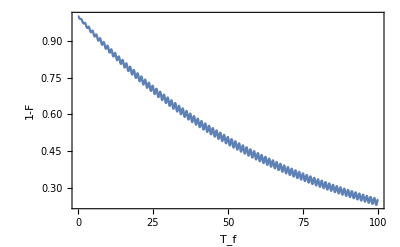

```mathematica
Plot[InfidFinal[Δl,Ωl,tfinal],{tfinal,0.01,100},PlotRange->All,Evaluate@font,Frame->True,FrameLabel->{"T_f","1-F"}]
```

### Infidelity In Log-Log scale

```mathematica
Plot[InfidFinal[Ωl,Δl,tfinal],{tfinal,1,10^5},PlotRange->All,ScalingFunctions->{"Log","Log"},PlotPoints->3,Evaluate@font,Frame->True,FrameLabel->MaTeX/@{"T_f","1-F"}]
```

### Result from the paper - fidelity dependence on Tf

```mathematica
(*Plot[FidFinal[Ωl,Δl,1/trev],{trev,0.001,1},PlotRange->All,PlotPoints->5,ScalingFunctions->"Log",Evaluate@font,Frame->True,FrameLabel->{"1/t_final","-log(F)"}]*)
```

# numerical results: Geodesic driving (half-sphere)

### Fidelity in time with error

### Probability of excitation for different final times

```mathematica
infidelityTfPlotNumerical=Plot[InfidFinal[Ω,Δ,tfinal],{tfinal,0.01,5},PlotRange->All,PlotPoints->50,Evaluate@font,Frame->True,PlotStyle->{Dashed,Red},FrameLabel->MaTeX/@{"T","F^*"},PlotLegends->Placed[{"numerical result"},{0.75,0.75}],ImageSize->450,AspectRatio->1/3];
```

### Infidelity dependence on Tf - loglog

```mathematica
infidelityTfPlotLogNumerical=Plot[InfidFinal[Ω,Δ,tfinal],{tfinal,0.01,10},PlotRange->All,ScalingFunctions->{"Log","Log"},PlotPoints->150,Evaluate@font,Frame->True,FrameLabel->MaTeX/@{"T","F^*"},PlotStyle->{Dashed,Red},PlotLegends->Placed[{"numerical result"},{0.14,0.15}],ImageSize->450,AspectRatio->1/3];
```

## Geodesical driving

```mathematica
σ={{{0,1},{1,0}},{{0,-I},{I,0}},{{1,0},{0,-1}}};
Hpurple[t_,Tf_]:={-s Cos[ω[Tf] t],0,s Sin[ω[Tf] t]}.σ
Hblue[t_,Tf_]:={{-ω[Tf]/2,-s},{-s,ω[Tf]/2}}
```

```mathematica
Hpurple[t,Tf]//MatrixForm
```

(10 Sin[(π t)/Tf] | -10 Cos[(π t)/Tf]
-10 Cos[(π t)/Tf] | -10 Sin[(π t)/Tf])

## Some calculations along the way

```mathematica
Hc[t_]:=d[t,10,100].σ
```

```mathematica
HH={-s Cos[ω t],0,s Sin[ω t]}.σ
MatrixExp[I ω t σ[[2]]/2].HH.MatrixExp[-I ω t σ[[2]]/2]//FullSimplify//MatrixForm
```

{{s Sin[t ω],-s Cos[t ω]},{-s Cos[t ω],-s Sin[t ω]}}

(0 | -s
-s | 0)

```mathematica
HH//MatrixForm
```

(s Sin[t ω] | -s Cos[t ω]
-s Cos[t ω] | -s Sin[t ω])

```mathematica
Eigensystem[HH]
```

{{-s,s},{{Sec[t ω]-Tan[t ω],1},{-Sec[t ω]-Tan[t ω],1}}}

```mathematica
Hblue={{-ω/2,-s},{-s,ω/2}};
Ublue=MatrixExp[-I Hblue t]//FullSimplify
```

{{Cos[1/2 t √(4 s^2+ω^2)]+(ⅈ ω Sin[1/2 t √(4 s^2+ω^2)])/(√(4 s^2+ω^2)),(2 ⅈ s Sin[1/2 t √(4 s^2+ω^2)])/(√(4 s^2+ω^2))},{(2 ⅈ s Sin[1/2 t √(4 s^2+ω^2)])/(√(4 s^2+ω^2)),Cos[1/2 t √(4 s^2+ω^2)]-(ⅈ ω Sin[1/2 t √(4 s^2+ω^2)])/(√(4 s^2+ω^2))}}

```mathematica
U=MatrixExp[-I ω t σ[[2]]/2].Ublue.MatrixExp[I ω t σ[[2]]/2]//FullSimplify
```

{{Cos[1/2 t √(4 s^2+ω^2)]+(ⅈ (ω Cos[t ω]-2 s Sin[t ω]) Sin[1/2 t √(4 s^2+ω^2)])/(√(4 s^2+ω^2)),(ⅈ (2 s Cos[t ω]+ω Sin[t ω]) Sin[1/2 t √(4 s^2+ω^2)])/(√(4 s^2+ω^2))},{(ⅈ (2 s Cos[t ω]+ω Sin[t ω]) Sin[1/2 t √(4 s^2+ω^2)])/(√(4 s^2+ω^2)),Cos[1/2 t √(4 s^2+ω^2)]+(ⅈ (-ω Cos[t ω]+2 s Sin[t ω]) Sin[1/2 t √(4 s^2+ω^2)])/(√(4 s^2+ω^2))}}

```mathematica
U//MatrixForm
```

```mathematica
({{Cos[q t]+(ⅈ (ω Cos[t ω]-2 s Sin[t ω]) Sin[qt])/(2q), (ⅈ (2 s Cos[t ω]+ω Sin[t ω]) Sin[qt])/(2q)}, {(ⅈ (2 s Cos[t ω]+ω Sin[t ω]) Sin[qt])/(2q), Cos[qt]+(ⅈ (-ω Cos[t ω]+2 s Sin[t ω]) Sin[qt])/(2q)}})
```

```mathematica
N@Det[Ublue/.{t->1,s->10,ω->10}]
```

1.

```mathematica
N@Norm[Ublue.{1,0}/.{t->1,s->10,ω->10}]
```

1.

```mathematica
{en,{eig0,eig1}}=Eigensystem[{{-ω/2,-s},{-s,ω/2}}]
```

{{-1/2 √(4 s^2+ω^2),1/2 √(4 s^2+ω^2)},{{-(-ω-√(4 s^2+ω^2))/(2 s),1},{-(-ω+√(4 s^2+ω^2))/(2 s),1}}}

```mathematica
MatrixExp[I t {{-ω/2,-s},{-s,ω/2}}]//FullSimplify
```

{{Cos[1/2 t √(4 s^2+ω^2)]-(ⅈ ω Sin[1/2 t √(4 s^2+ω^2)])/(√(4 s^2+ω^2)),-(2 ⅈ s Sin[1/2 t √(4 s^2+ω^2)])/(√(4 s^2+ω^2))},{-(2 ⅈ s Sin[1/2 t √(4 s^2+ω^2)])/(√(4 s^2+ω^2)),Cos[1/2 t √(4 s^2+ω^2)]+(ⅈ ω Sin[1/2 t √(4 s^2+ω^2)])/(√(4 s^2+ω^2))}}

```mathematica
which is for e=1/2 t q, q=√(4 s^2+ω^2)
```

```mathematica
{{Cos[e]-(ⅈ ω Sin[e])/q,-(2 ⅈ s Sin[e])/q},{-(2 ⅈ s Sin[e])/q,Cos[e]+(ⅈ ω Sin[e])/q}}
```

```mathematica
s=1;
ω[Tf_]:=π/Tf
d[t_,Tf_]:={-s Cos[ω[Tf]t],0,s Sin[ω[Tf]t]}
```

```mathematica
(*σ={{{0,1},{1,0}},{{0,-I},{I,0}},{{1,0},{0,-1}}};
d[t_,s_,Tf_]:={-s Cos[π t/Tf],0,s Sin[π t/Tf]}
Hc[t_,Tf_]:=d[t,Tf].σ*)
```

```mathematica
(*eigsOriginalFrame[t_,Tf_]:=Map[Normalize,Eigenvectors[Hc[t,Tf]]]*)
```

```mathematica
ens[Tf_]:=Eigenvalues[{{-ω[Tf]/2,-s},{-s,ω[Tf]/2}}]
eigs[Tf_]:=Eigenvectors[{{-ω[Tf]/2,-s},{-s,ω[Tf]/2}}]
psi[t_,Tf_]:=MatrixExp[-I/2 ω[Tf]t σ[[2]]].MatrixExp[I {{-ω[Tf]/2,-s},{-s,ω[Tf]/2}} t].{0,1}
(*ground[t_,Tf_]:=MatrixExp[-I/2 ω[Tf] t σ[[2]]].{0,1}*)
excitationProbability[t_,Tf_]:=Fidelity[{0,1},MatrixExp[I {{-ω[Tf]/2,-s},{-s,ω[Tf]/2}} t].{0,1}]
```

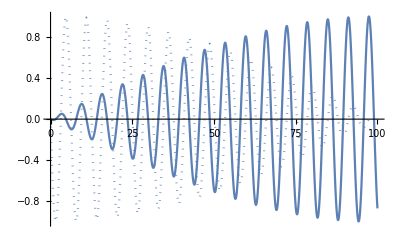

```mathematica
ReImPlot[psi[t,100][[1]],{t,0,100}]
```

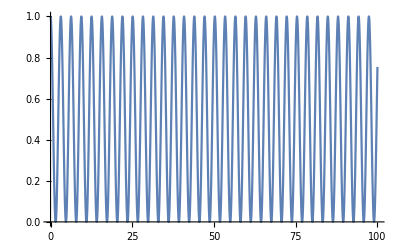

```mathematica
Plot[excitationProbability[t,100],{t,0,100}]
```

## Numerical results - Trash

Fidelity is time (t) and final time (Tf) dependent

```mathematica
s=10;
ω[Tf_]:=π/Tf
```

#### Purple basis

```mathematica
Upurple[t_,Tf_]:={{Cos[1/2 t √(4 s^2+ω[Tf]^2)]+(ⅈ ω[Tf] Sin[1/2 t √(4 s^2+ω[Tf]^2)])/(√(4 s^2+ω[Tf]^2)),(2 ⅈ s Sin[1/2 t √(4 s^2+ω[Tf]^2)])/(√(4 s^2+ω[Tf]^2))},{(2 ⅈ s Sin[1/2 t √(4 s^2+ω[Tf]^2)])/(√(4 s^2+ω[Tf]^2)),Cos[1/2 t √(4 s^2+ω[Tf]^2)]-(ⅈ ω[Tf] Sin[1/2 t √(4 s^2+ω[Tf]^2)])/(√(4 s^2+ω[Tf]^2))}}
```

```mathematica
groundStatepurple[t_,Tf_]:=eigSortedHfunction[Hpurple[t,Tf]][[1]]
psipurple[t_,Tf_]:=Upurple[t,Tf].groundStatepurple[0,Tf]
fpurple[t_,Tf_]:=Fidelity[groundStatepurple[t,Tf],psipurple[t,Tf]]
```

#### Blue basis

```mathematica
Ublue[t_,Tf_]:={{Cos[1/2 t √(4 s^2+ω[Tf]^2)]+(ⅈ (ω[Tf] Cos[t ω[Tf]]-2 s Sin[t ω[Tf]]) Sin[1/2 t √(4 s^2+ω[Tf]^2)])/(√(4 s^2+ω[Tf]^2)),(ⅈ (2 s Cos[t ω[Tf]]+ω[Tf] Sin[t ω[Tf]]) Sin[1/2 t √(4 s^2+ω[Tf]^2)])/(√(4 s^2+ω[Tf]^2))},{(ⅈ (2 s Cos[t ω[Tf]]+ω[Tf] Sin[t ω[Tf]]) Sin[1/2 t √(4 s^2+ω[Tf]^2)])/(√(4 s^2+ω[Tf]^2)),Cos[1/2 t √(4 s^2+ω[Tf]^2)]+(ⅈ (-ω[Tf] Cos[t ω[Tf]]+2 s Sin[t ω[Tf]]) Sin[1/2 t √(4 s^2+ω[Tf]^2)])/(√(4 s^2+ω[Tf]^2))}}
```

```mathematica
groundStateblue[t_,Tf_]:=eigSortedHfunction[Hblue[t,Tf]][[1]]
psiblue[t_,Tf_]:=Ublue[t,Tf].groundStateblue[0,Tf]
fblue[t_,Tf_]:=Fidelity[groundStateblue[t,Tf],psiblue[t,Tf]]
```

### Trash

### Infidelity in time - probability of excitation

```mathematica
f[t_,Tf_]:=fpurple[t,Tf]
```

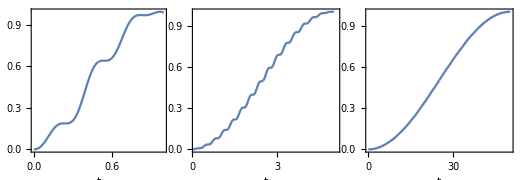

```mathematica
infidelityInTimePlot=plotGrid[
{{Plot[1-f[t,1],{t,0,1},PlotRange->{{0,1},All},Evaluate@font,Frame->True,FrameLabel->{"t","1-F"}],
Plot[1-f[t,5],{t,0,5},PlotRange->{{0.1,5.1},All},Evaluate@font,Frame->True,FrameLabel->{"t",""}],
Plot[1-f[t,50],{t,0,50},PlotRange->{{0.1,50},All},Evaluate@font,Frame->True,FrameLabel->{"t",""}]}},520,180,ImagePadding->45]
```

```mathematica
Export["/home/strelda/Documents/mff/dp/littleReports/twoLevelSystem/img/infidelityInTimePlot.pdf",infidelityInTimePlot,"AllowRasterization"->True,ImageResolution->800];
```

### Probability of non-excitation

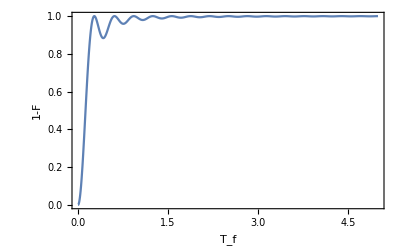

```mathematica
Plot[1-f[Tf,Tf],{Tf,0,5},PlotRange->All,Evaluate@font,Frame->True,FrameLabel->{"T_f","1-F"}]
```

```mathematica
Conjugate[psipurple[t,Tf]].Hpurple[t,Tf].Hpurple[t,Tf].psipurple[t,Tf]
```

```mathematica
N@enVarianceGeod[1,1]
```

3.93738

### Result from the paper - fidelity dependence on Tf

```mathematica
(*Plot[1-f[trev,trev],{trev,0.001,1},PlotRange->All,ScalingFunctions->{"Log","Log"},Evaluate@font,Frame->True,FrameLabel->{"1/t_final","1-F"}]*)
```

### Infidelity dependence on Tf - loglog

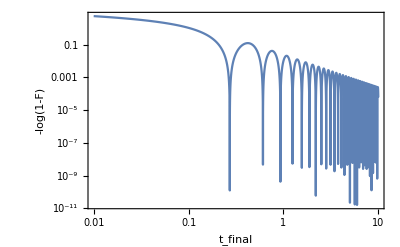

```mathematica
Plot[-Log[1-f[Tf,Tf]],{Tf,0.01,10},PlotRange->All,ScalingFunctions->{"Log","Log"},PlotPoints->1000,PerformanceGoal->"Quality",Evaluate@font,Frame->True,FrameLabel->{"t_final","-log(1-F)"}]
```

## Numerical derivation

```mathematica
Clear[s]
Clear[ω]
```

```mathematica
σ={{{0,1},{1,0}},{{0,-I},{I,0}},{{1,0},{0,-1}}};
d[t_,s_,Tf_]:={-s Cos[π t/Tf],0,s Sin[π t/Tf]}
```

```mathematica
Hpurple={{Ω,Δ},{Δ,-Ω}}
```

{{Ω,Δ},{Δ,-Ω}}

```mathematica
Hpurple/.{Δ->s Sin[t ω],Ω->-s Cos[t ω]}//MatrixForm
```

(-s Cos[t ω] | s Sin[t ω]
s Sin[t ω] | s Cos[t ω])

### Derivation of fidelity

```mathematica
Hblue1=FullSimplify[MatrixExp[-I ω/2 σ[[2]]t].Hpurple.MatrixExp[I ω/2 σ[[2]]t]+ω σ[[2]]/2]
```

{{Ω Cos[t ω]-Δ Sin[t ω],-(ⅈ ω)/2+Δ Cos[t ω]+Ω Sin[t ω]},{(ⅈ ω)/2+Δ Cos[t ω]+Ω Sin[t ω],-Ω Cos[t ω]+Δ Sin[t ω]}}

```mathematica
Hblue=FullSimplify[Hblue1/.{Δ->s Sin[t ω],Ω->-s Cos[t ω]}]
```

{{-s,-(ⅈ ω)/2},{(ⅈ ω)/2,s}}

```mathematica
Ublue=FullSimplify[MatrixExp[-I Hblue t],Assumptions->{ω>0,t>0,s>0}]
```

{{Cos[1/2 t √(4 s^2+ω^2)]+(2 ⅈ s Sin[1/2 t √(4 s^2+ω^2)])/(√(4 s^2+ω^2)),-(ω Sin[1/2 t √(4 s^2+ω^2)])/(√(4 s^2+ω^2))},{(ω Sin[1/2 t √(4 s^2+ω^2)])/(√(4 s^2+ω^2)),Cos[1/2 t √(4 s^2+ω^2)]-(2 ⅈ s Sin[1/2 t √(4 s^2+ω^2)])/(√(4 s^2+ω^2))}}

```mathematica
Upurple=FullSimplify[MatrixExp[I ω/2 σ[[2]]t].Ublue.MatrixExp[-I ω/2 σ[[2]]t]]
```

{{Cos[1/2 t √(4 s^2+ω^2)]+(2 ⅈ s Cos[t ω] Sin[1/2 t √(4 s^2+ω^2)])/(√(4 s^2+ω^2)),-((ω+2 ⅈ s Sin[t ω]) Sin[1/2 t √(4 s^2+ω^2)])/(√(4 s^2+ω^2))},{((ω-2 ⅈ s Sin[t ω]) Sin[1/2 t √(4 s^2+ω^2)])/(√(4 s^2+ω^2)),Cos[1/2 t √(4 s^2+ω^2)]-(2 ⅈ s Cos[t ω] Sin[1/2 t √(4 s^2+ω^2)])/(√(4 s^2+ω^2))}}

```mathematica
Ψpurplein=Normalize@Eigenvectors[Hpurple/.{Δ->s Sin[0 ω],Ω->-s Cos[0 ω]}][[1]]
```

{1,0}

```mathematica
Ψpurple=FullSimplify[Upurple.Ψpurplein]
```

{Cos[1/2 t √(4 s^2+ω^2)]+(2 ⅈ s Cos[t ω] Sin[1/2 t √(4 s^2+ω^2)])/(√(4 s^2+ω^2)),((ω-2 ⅈ s Sin[t ω]) Sin[1/2 t √(4 s^2+ω^2)])/(√(4 s^2+ω^2))}

```mathematica
groundStatepurple=FullSimplify[Normalize@Eigenvectors[Hpurple/.{Δ->s Sin[t ω],Ω->-s Cos[t ω]}][[1]],Assumptions->{ω>0,t>0,s>0}]
```

{-Cot[(t ω)/2]/(√(1+Abs[Cot[(t ω)/2]]^2)),1/(√(1+Abs[Cot[(t ω)/2]]^2))}

```mathematica
F=FullSimplify[Fidelity[groundStatepurple,Upurple.groundStatepurple],Assumptions->{ω>0,t>0,s>0,Tf>0}]
```

Norm[(Csc[(t ω)/2]^2 (Cos[1/2 t √(4 s^2+ω^2)]+(2 ⅈ s Sin[1/2 t √(4 s^2+ω^2)])/(√(4 s^2+ω^2))))/(1+Abs[Cot[(t ω)/2]]^2)]^2

```mathematica
Fsimplified=FullSimplify[((8 s^2+ω^2+ω^2 Cos[t √(4 s^2+ω^2)])/(2 (4 s^2+ω^2)))/(Sin[(t ω)/2]^4(1+Abs[Cot[(t ω)/2]]^2)^2)/.ω->π/Tf/.Tf->Subscript[T, f],Assumptions->{ω>0,t>0,s>0,Tf>0}]
```

(Csc[(π t)/(2 T_f)]^4 (π^2 (1+Cos[t √(4 s^2+π^2/T_f^2)])+8 s^2 T_f^2))/(2 (1+Abs[Cot[(π t)/(2 T_f)]]^2)^2 (π^2+4 s^2 T_f^2))

```mathematica
(Csc[(π t)/(2 Subscript[T, f])]^4 (π^2 (1+Cos[t √(4 s^2+π^2/Subscript[T, f]^2)])+8 s^2 Subscript[T, f]^2))/(2 (1+Abs[Cot[(π t)/(2 Subscript[T, f])]]^2)^2 (π^2+4 s^2 Subscript[T, f]^2))
```

#### Finding zero

```mathematica
(Csc[(π t)/(2 Subscript[T, f])]^4 (π^2 (1+Cos[t √(4 s^2+π^2/Subscript[T, f]^2)])+8 s^2 Subscript[T, f]^2))/(2 (1+Abs[Cot[(π t)/(2 Subscript[T, f])]]^2)^2 (π^2+4 s^2 Subscript[T, f]^2))==1
```

```mathematica
Csc[π/2]^4/(2 (1+Abs[Cot[π/2]]^2)^2)
```

1/2

```mathematica
(π^2 (1+Cos[√(T^2+π^2)])+2 T^2)/(2(π^2+T^2))==1
```

```mathematica
1+Cos[√(T^2+π^2)]==(2(π^2+T^2)-2 T^2)/π^2
```

```mathematica
Cos[√(T^2+π^2)]==1
```

Which has solution for k∈Z

```mathematica
√(T^2+π^2)=2k π
```

```mathematica
T=√((2k π)^2-π^2)
```

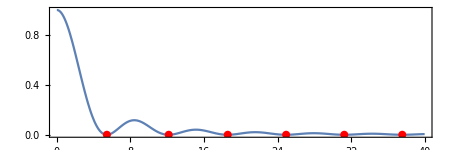

```mathematica
fidelityZeros=Show[Plot[1-(Csc[π/2]^4 (π^2 (1+Cos[ √(T^2+π^2)])+2 T^2))/(2 (1+Abs[Cot[π/2]]^2)^2 (π^2+T^2)),{T,0,40},Frame->True,Evaluate@font,PlotRange->All,FrameLabel->MaTeX/@{"T_s","1-F"}],ListPlot[Table[{√((2k π)^2-π^2),0},{k,1,6}],PlotStyle->Red],ImageSize->450,AspectRatio->1/3]
```

```mathematica
Export["/home/strelda/Documents/mff/dp/littleReports/twoLevelSystem/img/fidelityZeros.pdf",fidelityZeros,"AllowRasterization"->True,ImageResolution->800];
```

### In blue coordinate, F = 1 (counterdiabatic driving?)

```mathematica
Ψbluein=Normalize@Eigenvectors[Hblue/.{Δ->s Sin[0 ω],Ω->-s Cos[0 ω]}][[1]]
```

{(ⅈ (2 s+√(4 s^2+ω^2)))/(ω √(1+Abs[(2 s+√(4 s^2+ω^2))/ω]^2)),1/(√(1+Abs[(2 s+√(4 s^2+ω^2))/ω]^2))}

```mathematica
Ψblue=FullSimplify[Ublue.Ψbluein]
```

{(ⅈ ⅇ^(1/2 ⅈ t √(4 s^2+ω^2)) (2 s+√(4 s^2+ω^2)))/(ω √(1+Abs[(2 s+√(4 s^2+ω^2))/ω]^2)),(ⅇ^(1/2 ⅈ t √(4 s^2+ω^2)))/(√(1+Abs[(2 s+√(4 s^2+ω^2))/ω]^2))}

```mathematica
groundStateblue=FullSimplify[Normalize@Eigenvectors[Hblue/.{Δ->s Sin[t ω],Ω->-s Cos[t ω]}][[1]],Assumptions->{ω>0,t>0,s>0}]
```

{(ⅈ (2 s+√(4 s^2+ω^2)))/(ω √(1+((2 s+√(4 s^2+ω^2))^2)/ω^2)),1/(√(1+((2 s+√(4 s^2+ω^2))^2)/ω^2))}

```mathematica
Fblue=FullSimplify[Fidelity[groundStateblue,Ublue.groundStateblue],Assumptions->{ω>0,t>0,s>0,Tf>0}]
```

Norm[(ⅇ^(1/2 ⅈ t √(4 s^2+ω^2)) (2 s+√(4 s^2+ω^2)))/(√(ω^2+4 s (2 s+√(4 s^2+ω^2))))]^2

```mathematica
Fbluesimplified=FullSimplify[(ⅇ^(1/2 ⅈ t √(4 s^2+ω^2)) (2 s+√(4 s^2+ω^2)))/(√(ω^2+4 s (2 s+√(4 s^2+ω^2))))(ⅇ^(-1/2 ⅈ t √(4 s^2+ω^2)) (2 s+√(4 s^2+ω^2)))/(√(ω^2+4 s (2 s+√(4 s^2+ω^2))))]
```

1

### Energy variance

```mathematica
Ψpurple
```

{Cos[1/2 t √(4 s^2+ω^2)]+(2 ⅈ s Cos[t ω] Sin[1/2 t √(4 s^2+ω^2)])/(√(4 s^2+ω^2)),((ω-2 ⅈ s Sin[t ω]) Sin[1/2 t √(4 s^2+ω^2)])/(√(4 s^2+ω^2))}

```mathematica
enVarianceGeod=FullSimplify[Conjugate[Ψpurple].Hpurple.Hpurple.Ψpurple-(Conjugate[Ψpurple].Hpurple.Ψpurple)^2/.{Δ->s Sin[t ω],Ω->-s Cos[t ω]},Assumptions->{ω>0,t>0,s>0,Tf>0}]
```

(s^2 (16 s^4+14 s^2 ω^2+ω^4+2 s^2 ((-8 s^2+ω^2) Cos[2 t ω]-8 ω^2 Cos[t ω]^2 Cos[t √(4 s^2+ω^2)])-ω^2 (-2 s^2+(2 s^2+ω^2) Cos[2 t ω]) Cos[2 t √(4 s^2+ω^2)]+8 s^2 ω √(4 s^2+ω^2) Sin[2 t ω] Sin[t √(4 s^2+ω^2)]+ω^3 √(4 s^2+ω^2) Sin[2 t ω] Sin[2 t √(4 s^2+ω^2)]))/(2 (4 s^2+ω^2)^2)

```mathematica
s^2/(2 (4 s^2+ω^2)^2)(16 s^4+14 s^2 ω^2+ω^4+2 s^2 ((-8 s^2+ω^2) Cos[2 t ω]-8 ω^2 Cos[t ω]^2 Cos[t √(4 s^2+ω^2)])-ω^2 (-2 s^2+(2 s^2+ω^2) Cos[2 t ω]) Cos[2 t √(4 s^2+ω^2)]+8 s^2 ω √(4 s^2+ω^2) Sin[2 t ω] Sin[t √(4 s^2+ω^2)]+ω^3 √(4 s^2+ω^2) Sin[2 t ω] Sin[2 t √(4 s^2+ω^2)])
```

## Analytical results

```mathematica
Clear[s,ω]
```

```mathematica
s=10;
ω[Tf_]:=π/Tf
```

```mathematica
Fsimplified=FullSimplify[((8 s^2+ω^2+ω^2 Cos[t √(4 s^2+ω^2)])/(2 (4 s^2+ω^2)))/(Sin[(t ω)/2]^4(1+Abs[Cot[(t ω)/2]]^2)^2)/.ω->π/Tf/.Tf->Subscript[T, f],Assumptions->{ω>0,t>0,s>0,Tf>0}];
FidelityA[tA_,Tf_]:=Fsimplified/.{Subscript[T, f]->Tf,t->tA}
```

### fidelity in time with error

```mathematica
f[t_,Tf_]:=fpurple[t,Tf]
```

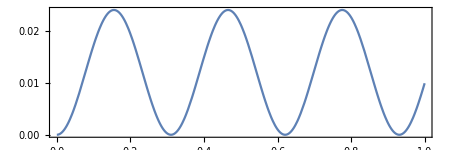

```mathematica
infidelityTimePlotGeod=Plot[1-FidelityA[t,1],{t,0,1},PlotRange->All,Evaluate@font,Frame->True,FrameLabel->MaTeX/@{"t","F^*"},ImageSize->450,AspectRatio->1/3]
```

```mathematica
Export["/home/strelda/Documents/mff/dp/dp_text/img/infidelityTimePlotGeod.pdf",infidelityTimePlotGeod,"AllowRasterization"->True,ImageResolution->800];
```

### fidelity on final time - probability of excitation

```mathematica
infidelityTfPlot=Plot[1-FidelityA[Tf,Tf],{Tf,0,5},PlotRange->All,Evaluate@font,Frame->True,FrameLabel->MaTeX/@{"T","F^*"},PlotLegends->Placed[{"from analytical formula"},{0.75,0.75}],ImageSize->450,AspectRatio->1/3];
```

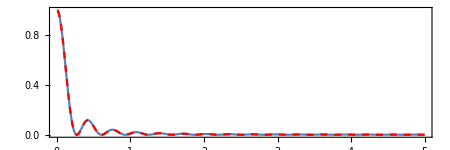

```mathematica
infidelityTfPlotC=Show[{infidelityTfPlot,infidelityTfPlotNumerical}]
```

```mathematica
Export["/home/strelda/Documents/mff/dp/dp_text//img/infidelityTfPlot.pdf",infidelityTfPlotC,"AllowRasterization"->True,ImageResolution->800];
```

### Fidelity dependence on Tf - loglog - probability of excitation

```mathematica
infidelityTfPlotLog=Plot[1-FidelityA[Tf,Tf],{Tf,0.01,10},PlotRange->All,ScalingFunctions->{"Log","Log"},PlotPoints->1000,PerformanceGoal->"Quality",Evaluate@font,Frame->True,FrameLabel->MaTeX/@{"T","F^*"},PlotLegends->Placed[{"from analytical formula"},{0.217,0.3}],ImageSize->450,AspectRatio->1/3];
```

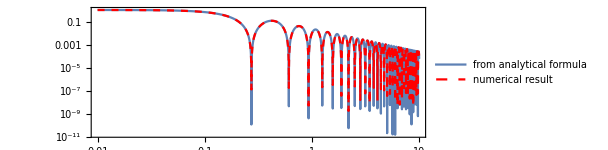

```mathematica
infidelityTfPlotLogC=Show[{infidelityTfPlotLog,infidelityTfPlotLogNumerical}]
```

```mathematica
Export["/home/strelda/Documents/mff/dp/dp_text/img/infidelityTfPlotLog.pdf",infidelityTfPlotLogC,"AllowRasterization"->True,ImageResolution->800];
```

### Density plots

```mathematica
dens3=DensityPlot[inFidelityLin[t,Tf,0.3],{t,0,100},{Tf,0,100},ScalingFunctions->{"Log","Log","Log"},Evaluate@densityPlotOptionstime,PlotPoints->140,Exclusions->None,ImageSize->270]
```

```mathematica
Export["/home/strelda/Documents/mff/dp/dp_text/img/dens3.pdf",dens3,"AllowRasterization"->True,ImageResolution->800];
```

### Energy variance

```mathematica
enVar[t_,Tf_]:=1/((π^2+400 Tf^2)^2)50 (π^4+1400 π^2 Tf^2+160000 Tf^4-π^2 Cos[2 t √(400+π^2/Tf^2)] (-200 Tf^2+(π^2+200 Tf^2) Cos[(2 π t)/Tf])+Tf (-1600 π^2 Tf Cos[t √(400+π^2/Tf^2)] Cos[(π t)/Tf]^2+200 Tf (π^2-800 Tf^2) Cos[(2 π t)/Tf]+2 π √(400+π^2/Tf^2) (400 Tf^2+π^2 Cos[t √(400+π^2/Tf^2)]) Sin[t √(400+π^2/Tf^2)] Sin[(2 π t)/Tf]));
```

```mathematica
densVar=DensityPlot[enVar[t,Tf],{t,1,100},{Tf,1,100},ScalingFunctions->{"Log","Log","Log"},Evaluate@densityPlotOptionstime,PlotPoints->600,Exclusions->None,ImageSize->270]
```

```mathematica
Export["/home/strelda/Documents/mff/dp/dp_text/img/densVar.pdf",densVar,"AllowRasterization"->True,ImageResolution->800];
```

```mathematica
enVarMax[Tf_,Ω_]:=FidelityA[Tf/2,Tf](1-FidelityA[Tf/2,Tf])(4 Ω^2)
enVarMax[Tf,Ω]//FullSimplify
```

(2 π^2 Ω^2 (π^2+800 Tf^2+π^2 Cos[1/2 √(400+π^2/Tf^2) Tf]) Sin[1/4 √(400+π^2/Tf^2) Tf]^2)/((π^2+400 Tf^2)^2)

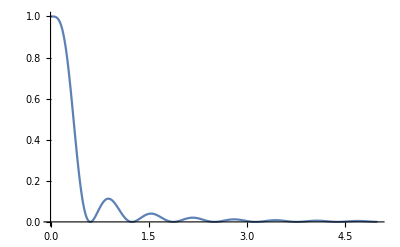

```mathematica
Plot[enVarMax[Tf,1],{Tf,0,5},PlotRange->All]
```

# Linear driving

## Zero state plot

```mathematica
Ωsc=10;
Δsc=1;
Ωf=Ωsc (-1+2 T/Tf);
```

```mathematica
zero=Simplify[Normalize@{(√(Δsc^2+(Ωsc (-1+(2 t)/Tf))^2)+Ωsc (-1+(2 t)/Tf))/Δsc,1},Assumptions->t>0];
```

```mathematica
zeroState=ReImPlot[zero[[2]]/.Tf->1,{t,0,1},Evaluate@plotOptionsBasic,FrameLabel->MaTeX/@{"t/T","\\alpha"}]
```

```mathematica
Export["/home/strelda/Documents/mff/dp/dp_text/img/zeroState.pdf",zeroState,"AllowRasterization"->True,ImageResolution->800];
```

## Analytical solution

Something for Laplace solution is not integrable here :(

```mathematica
Integrate[Tf/(2Ωs)(s a0+a0p)Exp[-s^3 Tf/(6Ωs)-I s-Δs^2 Tf/(2Ωs)s+2Tf s],s,Assumptions->{Tf>0,Δs>0}]
```

(Tf Integrate[ⅇ^(-ⅈ s+2 s Tf-(s^3 Tf)/(6 Ωs)-(s Tf Δs^2)/(2 Ωs)) (a0p+a0 s),s,Assumptions→{Tf>0,Δs>0}])/(2 Ωs)

```mathematica
fL[s_]:=(s -10I)/□
```

```mathematica
a=FullSimplify[InverseLaplaceTransform[fL[s],s,T]]
```

```mathematica
psi=FullSimplify[{a,√(1-a^2)},Assumptions->{T>0,Tf>T}]
```

```mathematica
ReImPlot[psi[[1]]/.Tf->100,{T,0,100}]
```

```mathematica
zero=Simplify[Normalize@{(√(Δsc^2+(Ωsc (-1+(2 T)/Tf))^2)+Ωsc (-1+(2 T)/Tf))/Δsc,1},Assumptions->T>0];
```

```mathematica
ReImPlot[zero/.Tf->100,{T,0,100}]
```

```mathematica
fff=Norm[psi zero]^2
```

```mathematica
Plot[fff/.Tf->100,{T,0,100}]
```

## DEF: inFidelityLinNonC[t,Tf,Ωconst], inFidelityLin[t,Tf,Ωconst], Hl[t, Tf, Ωconst], psi[t, Tf, Ωconst], enVariance[t, Tf, Ωconst]

```mathematica
inFidelityLinNonC[t_,Tf_,Ωconst_]:=Module[{Ω,Δ,sqr,qq,gam,Δfi,Δi,u,T,ui,en,ent,enti,om,Q0,Q1,Q00,Q10,n,a0t,b0t},
Ω[T_]:=Ωconst;
Δ[T_]:=Δl[T/Tf];
sqr=√(Tf^-1 Δfi);
om=Ω[0]/sqr;

Δfi=Δ[Tf]-Δ[0];
Δi=Δ[0];

u[T_]:=Δ[T]/sqr;
ui=u[0];
en[T_]:=Eigenvalues[H[Δ[T],Ω[T]]][[1]];
ent[T_]:=en[T]/sqr;

enti=ent[0];

(*Q0 and Q1 at initial time*)
qq=1/2 1/(√(enti(enti-om)));
Q00=qq(om-ui-enti);

Q10=qq(om+ui-enti);

n=(I om^2)/2;
gam=Gamma[1-n]/(√(2π));
a0t=gam(ParabolicCylinderD[n-1,(I-1)ui]Q00-(I+1)/om ParabolicCylinderD[n,(I-1)ui]Q10);
b0t=gam(ParabolicCylinderD[n-1,(1-I)ui]Q00+(I+1)/om ParabolicCylinderD[n,(1-I)ui]Q10);


Q0[T_]:=a0t ParabolicCylinderD[n,(1-I)u[T]]+b0t ParabolicCylinderD[n,(I-1)u[T]];
Q1[T_]:=-om/2(1-I)(a0t ParabolicCylinderD[n-1,(1-I)u[T]]-b0t ParabolicCylinderD[n-1,(I-1)u[T]]);
(*Real part needs to be added due to numerical error*)
Re[1/2(1+u[t]/ent[t])-u[t]/ent[t](Conjugate[Q0[t]]Q0[t]-om/u[t] Re[Conjugate[Q0[t]]Q1[t]])]

]
inFidelityLinNonEdited=Compile[{{t,_Real},{Tf,_Real},{Ωconst,_Real}},Module[{sqr,qc,gam,Ω,Δ,Δfi,Δi,u,T,ui,ent,enti,om,Q0,Q1,Q00,Q10,n,a0t,b0t},
Ωscale=10;
Δ=Ωscale (-1+2 t/Tf);

Δfi=2Ωscale;
sqr=√(Tf^-1 Δfi);
om=Ωconst/sqr;
Δi=-Ωscale;

u=Δ/sqr;
ui=Δi/sqr;
ent=(-√(Δ^2+Ωconst^2))/sqr;
enti=-(√(Ωscale^2+Ωconst^2))/sqr;

(*Q0 and Q1 at initial time*)
qc=1/2 1/(√(enti(enti-om)));
Q00=qc(om-ui-enti);
Q10=qc(om+ui-enti);

n=(I om^2)/2;
gam=Gamma[1-n]/(√(2π));
a0t=gam(ParabolicCylinderD[n-1,(I-1)ui]Q00-(I+1)/om ParabolicCylinderD[n,(I-1)ui]Q10);
b0t=gam(ParabolicCylinderD[n-1,(1-I)ui]Q00+(I+1)/om ParabolicCylinderD[n,(1-I)ui]Q10);


Q0=a0t ParabolicCylinderD[n,(1-I)u]+b0t ParabolicCylinderD[n,(I-1)u];
Q1=-om/2(1-I)(a0t ParabolicCylinderD[n-1,(1-I)u]-b0t ParabolicCylinderD[n-1,(I-1)u]);
(*Real part needs to be added due to numerical error*)
1/2(1+u/ent)-u/ent(Conjugate[Q0]Q0-om/u Re[Conjugate[Q0]Q1])

],CompilationTarget->"C",RuntimeOptions->"EvaluateSymbolically"->False]
inFidelityLin=Compile[{{t,_Real},{Tf,_Real},{Ωconst,_Real}},Module[{sqr,qc,gam,Ω,Δ,Δfi,Δi,u,T,ui,ent,enti,om,Q0,Q1,Q00,Q10,n,D1,D2,D3,D4},
Ωscale=10;
Δ=Ωscale (-1+2 t/Tf);

Δfi=2Ωscale;
sqr=√(Tf^-1 Δfi);
om=Ωconst/sqr;
Δi=-Ωscale;

u=Δ/sqr;
ui=Δi/sqr;
ent=(-√(Δ^2+Ωconst^2))/sqr;
enti=-(√(Ωscale^2+Ωconst^2))/sqr;

(*Q0 and Q1 at initial time*)
qc=1/2 1/(√(enti(enti-om)));
Q00=qc(om-ui-enti);
Q10=qc(om+ui-enti);

n=(I om^2)/2;
gam=Gamma[1-n]/(√(2π));

D1=ParabolicCylinderD[-1+n,(-1+ⅈ) ui];
D2=ParabolicCylinderD[n,(-1+ⅈ) ui];
D3=ParabolicCylinderD[-1+n,(1-ⅈ) ui];
D4=ParabolicCylinderD[n,(1-ⅈ) ui];
Q0=1/om(gam ParabolicCylinderD[n,(1-ⅈ) u] (om Q00 D1-(1+ⅈ) Q10 D2)+gam ParabolicCylinderD[n,(-1+ⅈ) u] (om Q00 D3+(1+ⅈ) Q10 D4));
Q1=1/2 (ParabolicCylinderD[-1+n,(1-ⅈ) u] ((-1+ⅈ) gam om Q00 D1+2 gam Q10 D2)+(1-ⅈ) gam ParabolicCylinderD[-1+n,(-1+ⅈ) u] (om Q00 D3+(1+ⅈ) Q10 D4));

1/(4ent(ent+om))Norm[Q0(ent+om-u)+Q1(ent+om+u)]^2

],CompilationTarget->"C"]



Hl=Compile[{{t,_Real},{Tf,_Real},{Ωconst,_Real}},Module[{Ω,Δ},
Ω=Ωconst;
Δ=Ωscale (-1+2 t/Tf);
{{Ω,Δ},{Δ,-Ω}}
],CompilationTarget->"C",RuntimeOptions->"EvaluateSymbolically"->False]
psi=Compile[{{t,_Real},{Tf,_Real},{Ωconst,_Real}},Module[{sqr,qc,gam,Ω,Δ,Δfi,Δi,u,T,ui,ent,enti,om,Q0,Q1,Q00,Q10,n,a0t,b0t},
Ωscale=10;
Δ=Ωscale (-1+2 t/Tf);

Δfi=2Ωscale;
sqr=√(Tf^-1 Δfi);
om=Ωconst/sqr;
Δi=-Ωscale;

u=Δ/sqr;
ui=Δi/sqr;
ent=(-√(Δ^2+Ωconst^2))/sqr;
enti=-(√(Ωscale^2+Ωconst^2))/sqr;

(*Q0 and Q1 at initial time*)
qc=1/2 1/(√(enti(enti-om)));
Q00=qc(om-ui-enti);
Q10=qc(om+ui-enti);

n=(I om^2)/2;
gam=Gamma[1-n]/(√(2π));
a0t=gam(ParabolicCylinderD[n-1,(I-1)ui]Q00-(I+1)/om ParabolicCylinderD[n,(I-1)ui]Q10);
b0t=gam(ParabolicCylinderD[n-1,(1-I)ui]Q00+(I+1)/om ParabolicCylinderD[n,(1-I)ui]Q10);


Q0=a0t ParabolicCylinderD[n,(1-I)u]+b0t ParabolicCylinderD[n,(I-1)u];
Q1=-om/2(1-I)(a0t ParabolicCylinderD[n-1,(1-I)u]-b0t ParabolicCylinderD[n-1,(I-1)u]);
1/(√2){Q1+Q0,Q1-Q0}

],CompilationTarget->"C",RuntimeOptions->"EvaluateSymbolically"->False]
enVariance[t_,Tf_,Ωconst_]:=Module[{p,h},
p=psi[t,Tf,Ωconst];
h=Hl[t,Tf,Ωconst];
Re[Conjugate[p].h.h.p-(Conjugate[p].h.p)^2]
]
```

CompiledFunction[…]

CompiledFunction[…]

CompiledFunction[…]

«1 more identical outputs»

## Final fidelity on Δ - density plots

```mathematica
dens2=DensityPlot[inFidelityLin[Tf,Tf,Ωconst],{Ωconst,0.5,4},{Tf,1,500},ScalingFunctions->"Log",PlotRange->{10^-15,1},Evaluate@densityPlotOptionsBasic,FrameLabel->MaTeX/@{"\\Delta","T"},PlotPoints->300,Exclusions->None,ImageSize->270]
```

```mathematica
Export["/home/strelda/Documents/mff/dp/dp_text/img/dens2.pdf",dens2,"AllowRasterization"->True,ImageResolution->800];
```

```mathematica
dens2Zoom=DensityPlot[inFidelityLin[Tf,Tf,Ωconst],{Ωconst,2,8},{Tf,1,4},ScalingFunctions->"Log",Evaluate@densityPlotOptionsBasic,FrameLabel->MaTeX/@{"\\Delta","T"},PlotPoints->100,Exclusions->None,ImageSize->270]
```

```mathematica
Export["/home/strelda/Documents/mff/dp/dp_text/img/dens2Zoom.pdf",dens2Zoom,"AllowRasterization"->True,ImageResolution->800];
```

## Energy variance

```mathematica
densVariance=DensityPlot[enVariance[t,Tf,1],{t,0,100},{Tf,0,100},ScalingFunctions->{"Log","Log","Log"},Evaluate@densityPlotOptionstime,PlotPoints->200,Exclusions->None,ImageSize->270]
```

```mathematica
Export["/home/strelda/Documents/mff/dp/dp_text/img/densVariance.pdf",densVariance,"AllowRasterization"->True,ImageResolution->800];
```

```mathematica
contVariance=ContourPlot[enVariance[Tf/2,Tf,Ω],{Tf,1,10},{Ω,0.01,10},PlotPoints->200,Evaluate@densityPlotOptionsBasic,FrameLabel->MaTeX/@{"T","\\Omega"},Contours->30,ImageSize->270]
```

```mathematica
Export["/home/strelda/Documents/mff/dp/dp_text/img/contVariance.pdf",contVariance,"AllowRasterization"->True,ImageResolution->800];
```

```mathematica
Plot[enVariance[Tf/2,Tf,1],{Tf,1,500},ScalingFunctions->{"Log","Log"},Evaluate@plotOptionsBasic,FrameLabel->MaTeX/@{"T_f","\\delta E^2"}]
```

## Fidelity in time and final time dependence

### Infidelity in time with error

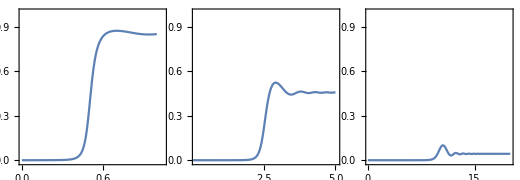

```mathematica
infidelityInTimePlot=plotGrid[
{{Plot[inFidelityLin[t,1,1],{t,0,1},PlotRange->{{0,1.05},{-0.01,1}},Evaluate@font,Frame->True,FrameLabel->MaTeX/@{"t","F^*"},PlotPoints->30],
Plot[inFidelityLin[t,5,1],{t,0,5},PlotRange->{{0.1,5.05},{-0.01,1}},Evaluate@font,Frame->True,FrameLabel->MaTeX/@{"t","F^*"},PlotPoints->30],
Plot[inFidelityLin[t,20,1],{t,0,20},PlotRange->{{0.1,20},{-0.01,1}},Evaluate@font,Frame->True,FrameLabel->MaTeX/@{"t","F^*"},PlotPoints->30]}},520,180,ImagePadding->45]
```

```mathematica
Export["/home/strelda/Documents/mff/dp/dp_text/img/infidelityInTimePlot1.pdf",infidelityInTimePlot,"AllowRasterization"->True,ImageResolution->800];
```

Once the oscillations occur, they do not disappear (property of the system of linear equations)

```mathematica
slowPlot=Plot[inFidelityLin[t,100,1] 10^4,{t,1,100},Evaluate@plotOptionsBasic,FrameLabel->MaTeX/@{"t","F^*\\cdot 10^4"},PlotPoints->50]
```

```mathematica
slowPlotZoom1=Plot[10^12 inFidelityLin[t,80,1],{t,45,60},Evaluate@plotOptionsBasic,FrameLabel->MaTeX/@{"t","F^*\\cdot 10^{12}"},PlotPoints->10,FrameTicks->{{{1,2,3},None},{{2600,2650,2700},None}}]
```

```mathematica
undercritical=Plot[inFidelityLin[t,80,1] 10^6,{t,75,80},Evaluate@plotOptionsBasic,FrameLabel->MaTeX/@{"t","F^*\\cdot 10^{6}"},PlotPoints->50]
```

```mathematica
Export["/home/strelda/Documents/mff/dp/dp_text/img/undercritical.pdf",undercritical,"AllowRasterization"->True,ImageResolution->800];
```

```mathematica
overcritical=Plot[inFidelityLin[t,170,1] 10^9,{t,165,170},Evaluate@plotOptionsBasic,FrameLabel->MaTeX/@{"t","F^*\\cdot 10^{9}"},PlotPoints->50]
```

```mathematica
Export["/home/strelda/Documents/mff/dp/dp_text/img/overcritical.pdf",overcritical,"AllowRasterization"->True,ImageResolution->800];
```

```mathematica
slowinfidCombined=Overlay[{slowPlot,Item[Show[slowPlotZoom1,ImageSize->190],Alignment->{-.75,.8}],Item[Show[slowPlotZoom2,ImageSize->190],Alignment->{.32,.8}]}]
```

Show::gtype: Symbol is not a type of graphics.

```mathematica
Export["/home/strelda/Documents/mff/dp/dp_text/img/slowinfidCombined.pdf",slowinfidCombined,"AllowRasterization"->True,ImageResolution->800];
```

#### Fourier transform

```mathematica
Needs["FourierSeries`"]
```

```mathematica
fourierInfidelityLin[ω_]:=NFourierTransform[inFidelityLin[t,3000,0.3],t,ω]
```

```mathematica
Quiet@fourierInfidelityLin[0.01]
```

3.24829×10^144-6.13448×10^140 ⅈ

```mathematica
fourierTab=Quiet@ParallelTable[Evaluate@fourierInfidelityLin[ω],{ω,0,10,1}]
```

$Aborted

```mathematica
ListPlot[fourierTab]
```

### Infidelity on final time - probability of excitation

```mathematica
infidelityTfPlot=Plot[inFidelityLin[Tf,Tf,0.3],{Tf,0,1000},PlotRange->All,Evaluate@font,Frame->True,FrameLabel->MaTeX/@{"T","F^*"},AspectRatio->1/3,ImageSize->460,ImageSize->450,AspectRatio->1/3];
```

```mathematica
infidelityTfPlotLogLin=Plot[inFidelityLin[Tf,Tf,1],{Tf,1,1000},PlotRange->All,ScalingFunctions->{"Log","Log"},PerformanceGoal->"Quality",PlotPoints->1000,Evaluate@font,Frame->True,FrameLabel->MaTeX/@{"T","F^*"},AspectRatio->1/3,ImageSize->460];
```

```mathematica
infidelityTfPlotLogLinZoom=Plot[inFidelityLin[Tf,Tf,1],{Tf,115,125},PlotRange->All,ScalingFunctions->{"Log","Log"},PerformanceGoal->"Quality",PlotPoints->1000,Evaluate@font,Frame->True,FrameLabel->MaTeX/@{"T","F^*"},AspectRatio->1/3,ImageSize->460];
```

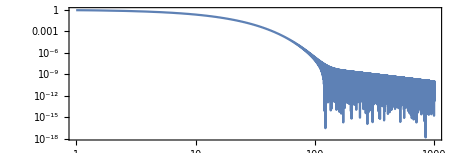
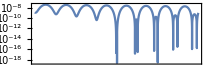

```mathematica
infidelityTfPlotLogLinCombined=Overlay[{infidelityTfPlotLogLin,Item[Show[infidelityTfPlotLogLinZoom,ImageSize->210],Alignment->{-.6,.45}]}]
```

```mathematica
Export["/home/strelda/Documents/mff/dp/text_dp/img/infidelityTfPlotLogLinCombined1.pdf",infidelityTfPlotLogLinCombined,"AllowRasterization"->True,ImageResolution->800];
```

### Averaging final Infidelity

```mathematica
finalAveragedInfidelity[Tf_,finalCut_]:=1/(finalCut Tf)NIntegrate[inFidelityLinNonC[tf,Tf,1],{tf,(1-finalCut) Tf,Tf}]
```

```mathematica
infidelityTfPlotLogAveraged=Plot[finalAveragedInfidelity[Tf,0.1],{Tf,1,1000},PlotRange->All,ScalingFunctions->{"Log","Log"},PerformanceGoal->"Quality",PlotPoints->100,Evaluate@font,Frame->True,FrameLabel->MaTeX/@{"T","\\langle F^*\\rangle _{0.9}"},AspectRatio->1/3,ImageSize->460];
```

```mathematica
infidelityTfPlotLogAveragedZoom=Plot[finalAveragedInfidelity[Tf,0.1] 10^7,{Tf,100,140},PlotRange->All,PerformanceGoal->"Quality",PlotPoints->100,Evaluate@font,Frame->True,FrameLabel->MaTeX/@{"T","\\langle F^*\\rangle _{0.9}\\cdot 10^7"},AspectRatio->1/3,ImageSize->460];
```

```mathematica
infidCombined=Overlay[{infidelityTfPlotLogAveraged,Item[Show[infidelityTfPlotLogAveragedZoom,ImageSize->210],Alignment->{-.6,.42}]}]
```

```mathematica
Export["/home/strelda/Documents/mff/dp/dp_text/img/infidCombined1.pdf",infidCombined,"AllowRasterization"->True,ImageResolution->800];
```

### Landau - Zener

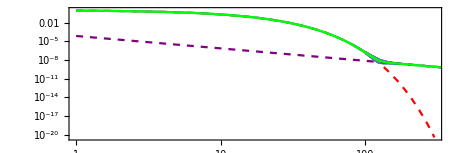

```mathematica
lz[Tf_]:=Exp[-π Tf 1^2/20]
lzPlot=Plot[lz[Tf],{Tf,1,300},ScalingFunctions->{"Log","Log"},PlotStyle->{Red,Dashed},Evaluate@font,Frame->True,FrameLabel->MaTeX/@{"T_f","\\langle F^*\\rangle _{0.9}"},AspectRatio->1/3,ImageSize->460];
linearPlot=Plot[Exp[Log[Tf^-2]-Log[14000]],{Tf,1,1000},ScalingFunctions->{"Log","Log"},PlotStyle->{Purple,Dashed}];
sumPlot=Plot[lz[Tf]+Exp[Log[Tf^-2]-Log[14000]],{Tf,1,1000},ScalingFunctions->{"Log","Log"},PlotStyle->{Green}];
landauComparePlot=Show[lzPlot,infidelityTfPlotLogAveraged,linearPlot,sumPlot]
```

```mathematica
Export["/home/strelda/Documents/mff/dp/dp_text/img/landauCompare.pdf",landauComparePlot,"AllowRasterization"->True,ImageResolution->800];
```

### Infidelity peak dependence on Tf

```mathematica
pltTf[Tf_]:=Plot[inFidelityLin[t,Tf,1],{t,Tf 0.55,Tf 0.7},PlotPoints->10,PlotRange->All,ImageSize->Medium]
```

```mathematica
Table[pltTf[tf],{tf,10,100,10}]
```

```mathematica
Plot[inFidelityLin[Tf,Tf,1],{Tf,1,500},PlotRange->All,ScalingFunctions->{"Log","Log"},PerformanceGoal->"Quality",PlotPoints->50,Evaluate@font,Frame->True,FrameLabel->MaTeX/@{"T_f","1-F"},AspectRatio->1/3,ImageSize->460]
```

Formula has no physical meaning for t > Tf, but for t -> ∞, it has a meaning of the mean oscillation value:

```mathematica
Plot[inFidelityLin[10Tf,Tf,1],{Tf,1,500},PlotRange->All,ScalingFunctions->{"Log","Log"},PerformanceGoal->"Quality",PlotPoints->50,Evaluate@font,Frame->True,FrameLabel->MaTeX/@{"T_f","1-F"},AspectRatio->1/3,ImageSize->460]
```

## All together - Final fidelity Density Plots with marks and references to plots

```mathematica
undercriticalLINE=Rotate[Plot[inFidelityLin[t,80,1] 10^6,{t,75,80},PlotPoints->10,ImageSize->130,Evaluate@font,Ticks->None,AxesLabel->MaTeX/@{"t","F^*"}],π/2]
```

-Graphics-

```mathematica
overcriticalLINE=Rotate[Plot[inFidelityLin[t,170,1] 10^9,{t,165,170},PlotPoints->10,ImageSize->130,Ticks->None,Evaluate@font,AxesLabel->MaTeX/@{"t","F^*"}],π/2]
```

-Graphics-

```mathematica
dens2=DensityPlot[inFidelityLin[t,Tf,1],{Tf,0.1,200},{t,0.1,200},ScalingFunctions->"Log",PlotRange->{10^-15,1},Evaluate@densityPlotOptionsBasic,FrameLabel->MaTeX/@{"T","t"},PlotPoints->300,Exclusions->None,ImageSize->410];
```

```mathematica
allInOne=Overlay[{Overlay[{Show[{
dens2,
ListLinePlot[{{0,0},{200,200}},PlotStyle->Black],
ListLinePlot[{{0,0},{200,100}},PlotStyle->{Black,Dashed}],
ListLinePlot[{{120,0},{120,200}},PlotStyle->{Purple,Dashed}],
ListLinePlot[{{80,0},{80,80}},PlotStyle->{Lighter[Blue],Opacity[0.3]}],
ListLinePlot[{{80,75},{80,80}},PlotStyle->{Lighter[Blue]}],
ListLinePlot[{{170,0},{170,170}},PlotStyle->{Lighter[Blue],Opacity[0.3]}],
ListLinePlot[{{170,165},{170,170}},PlotStyle->{Lighter[Blue]}],
Graphics[{Lighter@Blue,Arrow[{{50,160},{167 ,168}}]}],
Graphics[{Lighter@Blue,Arrow[{{50,80},{78,78}}]}]
}],
undercriticalLINE},Alignment->{-0.75,-0.1}],overcriticalLINE},Alignment->{-0.75,0.85}]
```

```mathematica
Export["/home/strelda/Documents/mff/dp/dp_text/img/allInOne.pdf",allInOne,"AllowRasterization"->True,ImageResolution->800];
```

## Harmonic oscillator correspondence

```mathematica
gamma[t_,Ω_,Δ_]:=I Ω-D[Δ,T]/Δ-I Δ Ω/.T->t
omega2[t_,Ω_,Δ_]:=I D[Ω,T]-I Ω D[Δ,T]/Δ- Δ Ω^2/.T->t
```

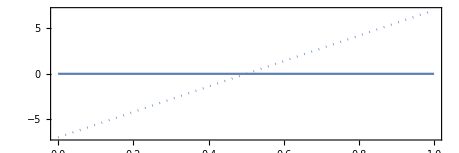

```mathematica
ReImPlot[gamma[t,Δl[T],Ωl[T]],{t,0,1},Evaluate@plotOptionsBasic]
```

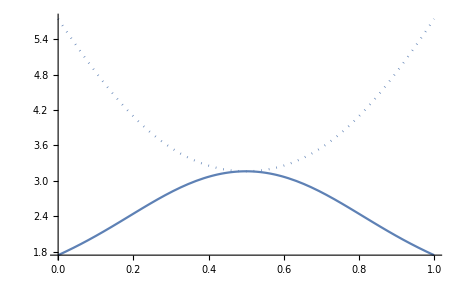

```mathematica
ReImPlot[Sqrt@omega2[t,Δl[T],Ωl[T]],{t,0,1}]
```

Harmonic oscillator equation at the points F = 1 for linear driving

```mathematica
difka=x''[t]+(Ω I+2/(Tf-2t)+10Ω(1-(2t)/Tf))x'[t]+(I Ω 2/(Tf-2t)-10(1-2 t/Tf)Ω^2)x[t]==0
```

((2 ⅈ Ω)/(-2 t+Tf)-10 (1-(2 t)/Tf) Ω^2) x[t]+(2/(-2 t+Tf)+ⅈ Ω+10 (1-(2 t)/Tf) Ω) x'[t]+x''[t]==0

## Some regressions and random dependences

### Checking the Tc=Tc(Ω) dependence manually

#### Plots

```mathematica
critTimeOnEnPlots=ParallelMap[Plot[-Log[1-inFidelityLin[Tf,Tf,#]],{Tf,1,10^4},PlotRange->All,ScalingFunctions->{"Log","Log"},PlotPoints->3,Evaluate@font,Frame->True,FrameLabel->{"t_final","-log(F)"}]&,Range[0.1,2,0.1]]
```

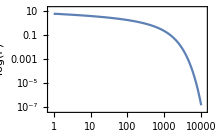
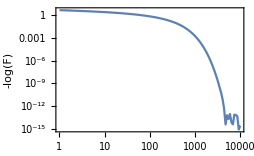
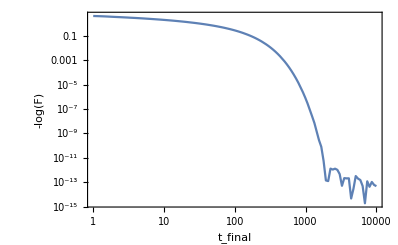
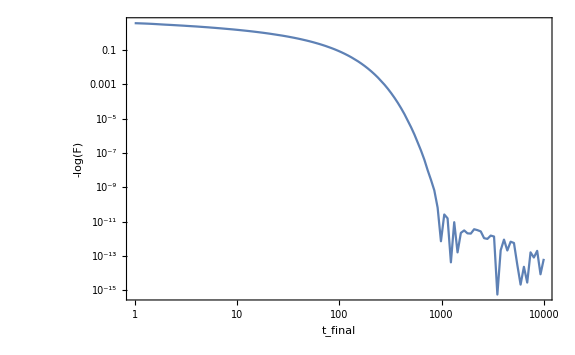
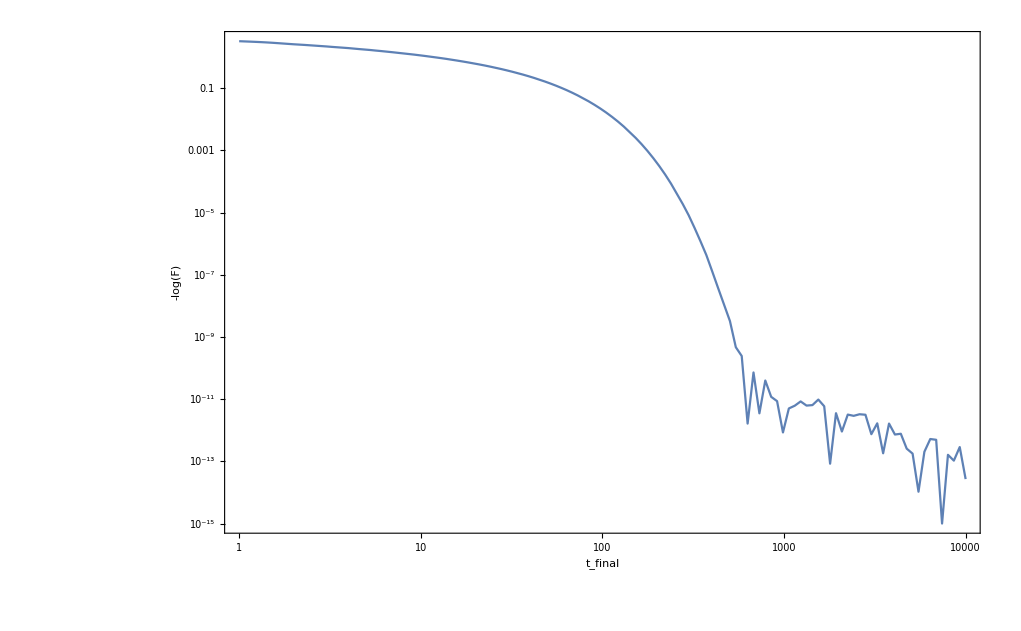
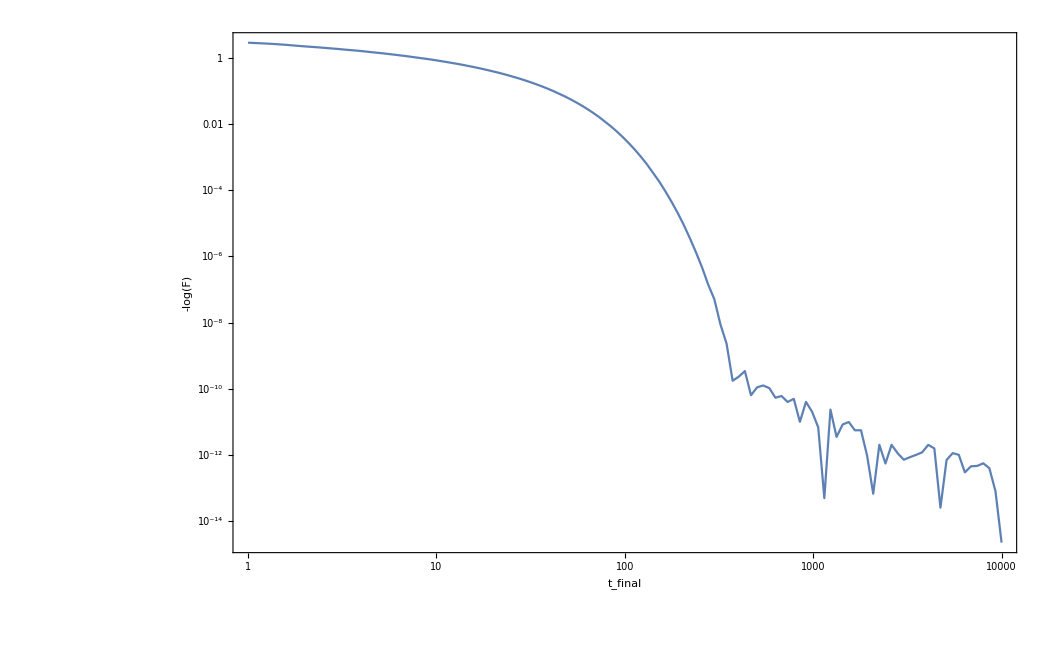
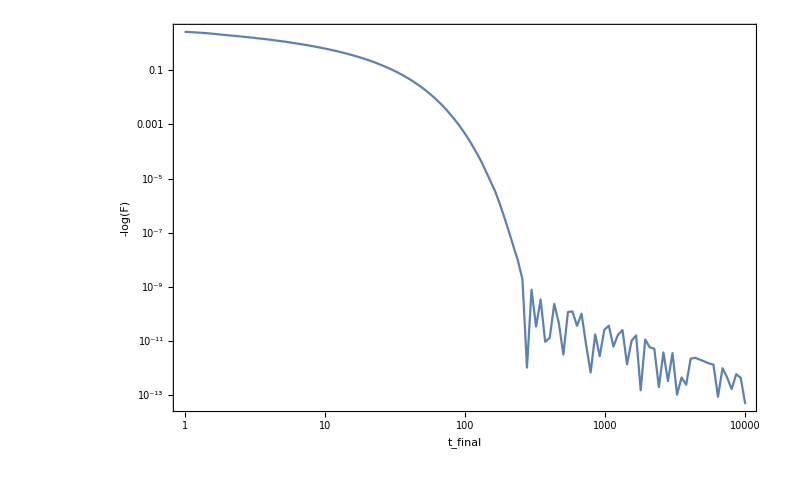
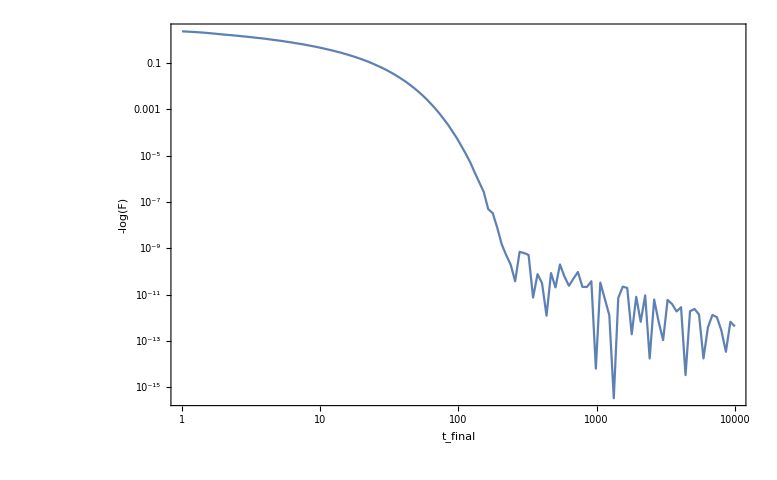

#### From plots - Tc=Tc(Ωconst)

From plots above, the coordinates (Ω_crit;T_crit) was written out

```mathematica
TcOmega={{0.2,4700},{0.3,2100},{0.4,1000},{0.5,650},{0.6,390},{0.7,280},{0.8,260},{0.9,175},{1.0,142},{1.1,95},{1.2,71},{1.3,61},{1.4,50},{1.5,40},{1.6,39},{1.7,31},{1.8,29},{1.9,23},{2.0,22}};
```

185.158/om^2

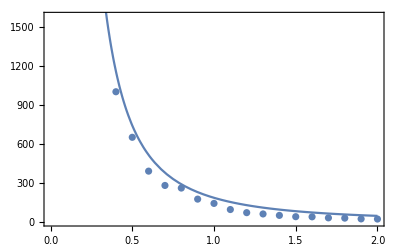

```mathematica
TcOmegaFit=Fit[TcOmega,{om^-2},om]
Show[{ListPlot[TcOmega,Frame->True,FrameLabel->MaTeX/@{"\\Omega","T_c"}],Plot[TcOmegaFit,{om,0.2,2.0}]}]
```

### Tc=Tc(ΔE_01)

#### From Hamiltonian - energy difference ΔE_01 on Ωconst

```mathematica
ΔE01[Ω_]:=2 √(0^2+Ω^2)
```

```mathematica
TcOnΔE01=FullSimplify[TcFromRootFit/.om->ΔE01/2]
```

```mathematica
Plot[TcOnΔE01,{ΔE01,0.1,3},Frame->True,PlotRange->All,FrameLabel->MaTeX/@{"\\Delta E_{01}","T_c"}]
```

### δE^2=δE^2(Ωconst(ΔE_01))

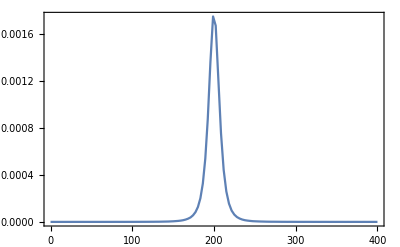
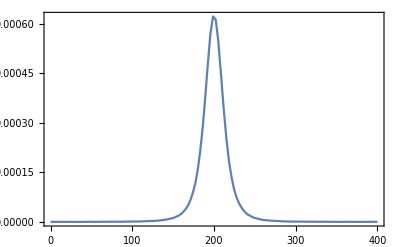
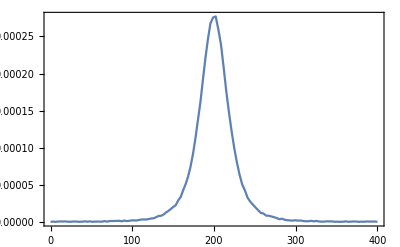

```mathematica
Plot[enVariance[t,400,#],{t,0,400},Evaluate@font,Frame->True,FrameLabel->MaTeX/@{"t","\\delta E^2"},PlotRange->All,PlotPoints->3]&/@{0.6,1,1.5}
```

#### δE^2=δE^2(Ω) for T_c=T_f and t=T_c/2

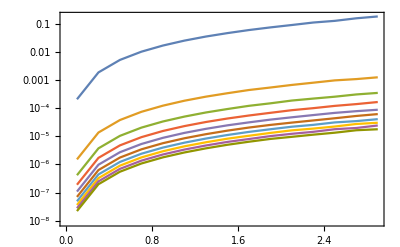

```mathematica
ListLinePlot[Table[ParallelTable[{Ω,enVariance[a Tc[Ω]/2,a Tc[Ω],Ω]},{Ω,0.1,3,0.2}],{a,0.1,10,1}],ScalingFunctions->"Log",Frame->True,FrameLabel->MaTeX/@{"\\Omega","\\delta E^2"}]
```

```mathematica
Plot[enVariance[Tc/2,Tc,2],{Tc,0.1,10}]
```

$Aborted

{{0.1,3.14868×10^-6},{0.2,0.0000125948},{0.3,0.0000283367},{0.4,0.0000503735},{0.5,0.0000786993},{0.6,0.000113368},{0.7,0.000154283},{0.8,0.000201315},{0.9,0.000255072},{1.,0.000315486},{1.1,0.000380638},{1.2,0.000454841},{1.3,0.00053024},{1.4,0.000615732},{1.5,0.000711342},{1.6,0.000800626},{1.7,0.000916053},{1.8,0.00102962},{1.9,0.00112845},{2.,0.00125305},{2.1,0.0013754},{2.2,0.00149872},{2.3,0.00164915},{2.4,0.00182478},{2.5,0.00201793},{2.6,0.00209577},{2.7,0.00225335},{2.8,0.00253062},{2.9,0.0027008},{3.,0.00289496}}

0.000316847 Ω^2

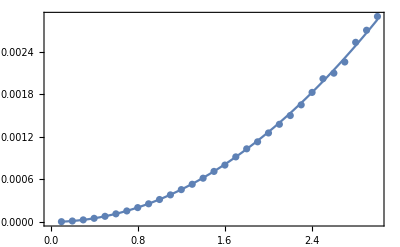

```mathematica
enVarianceTcTab=ParallelTable[{Ω,enVariance[(4a)/(2 Ω^2),(4a)/Ω^2,Ω]},{Ω,0.1,3,0.1}]
enVarianceTcFit=Fit[enVarianceTcTab,{Ω^2},Ω]
Show[{
ListPlot[enVarianceTcTab,Frame->True,FrameLabel->MaTeX/@{"\\Omega","\\delta E^2"}],
Plot[enVarianceTcFit,{Ω,0.1,3}]
}]
```

#### Max δE^2=δE^2|_(t=Tc/2)=δE^2(t=Tc/2,T_f,Ω)

```mathematica
maxVarianceTfTab=ParallelTable[{Tf,enVariance[Tf/2,Tf,2]},{Tf,60,5000,50}];
```

116.833/Tf^2

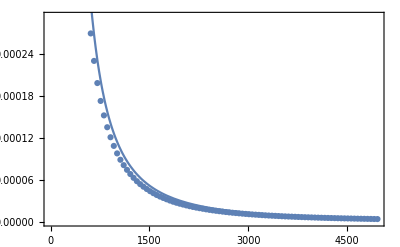

```mathematica
maxVarianceTfFit=Fit[maxVarianceTfTab,{Tf^-2},Tf]
Show[{
ListPlot[maxVarianceTfTab,Frame->True,FrameLabel->MaTeX/@{"T_f","\\delta E^2\\big|_{t=T_f/2}"}],
Plot[maxVarianceTfFit,{Tf,60,5000}]
}]
```

114.94/omega^2

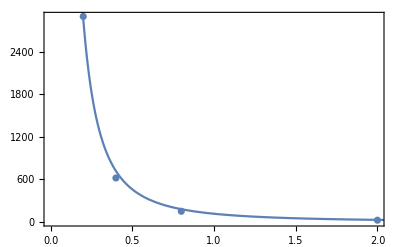

```mathematica
konstOmegaTab={{0.2,2900},{0.4,620},{0.8,150},{2,24}};
konstOmegaFit=Fit[konstOmegaTab,{omega^-2},omega]
Show[{ListPlot[konstOmegaTab,Frame->True,FrameLabel->MaTeX/@{"\\Omega","konst"}],
Plot[konstOmegaFit,{omega,0.02,3},PlotRange->All]}]
```

Fit does not converge sometimes, but putting it all together, we get approximation for konst=115/Ω^2 for Ω∈[0.2,3]

```mathematica
Ωtest=0.2;
maxVarianceTfTab=ParallelTable[{Tf,enVariance[Tf/2,Tf,Ωtest]},{Tf,60,5000,50}];
Manipulate[Show[{
ListPlot[maxVarianceTfTab,Frame->True,FrameLabel->MaTeX/@{"T_f","\\Delta E^2\\big|_{t=T_f/2}"}],
Plot[a/Tf^2,{Tf,60,5000},PlotStyle->Red]
}],{{a,110/Ωtest^2},10,3000}]
```

Therefore ΔE_01(T_f)=110/(Ω^2 T_f^2)for Ω∈[0.2,3]

#### Some plots for fun

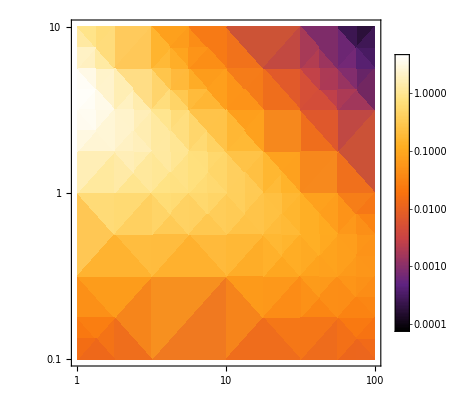

```mathematica
DensityPlot[enVariance[Tf/2,Tf,const],{Tf,1,10^2},{const,0.1,10},ScalingFunctions->{"Log","Log","Log"},Evaluate@densityPlotOptionsParam,PlotPoints->5,Exclusions->None]
```

```mathematica
(*densVarianceTab=Flatten[ParallelTable[{t,Tf,enVariance[t,Tf,0.2]},{t,1,1000,10},{Tf,1,10,2}],1];
ListDensityPlot[densVarianceTab,ScalingFunctions->{"Log","Log","Log"},Evaluate@densityPlotOptionsParam]*)
```

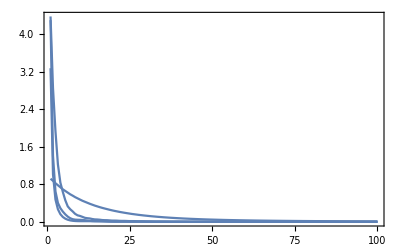

```mathematica
Plot[enVariance[Tf/2,Tf,#]&/@{1,3,5,7},{Tf,1,100},Evaluate@font,Frame->True,FrameLabel->MaTeX/@{"t","\\Delta E^2"},PlotRange->All,PlotPoints->3]
```

```mathematica
enVariance[10^3/2,10^3,1]
```

0.000100207

```mathematica
tab1=Flatten[ParallelTable[{Tf,omega,enVariance[Tf/2,Tf,omega]},{Tf,1,10^4,1000},{omega,0.1,2,0.1}],1]
```

$Aborted

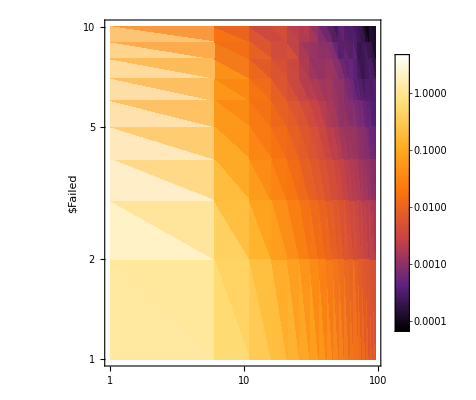

```mathematica
ListDensityPlot[tab1,ScalingFunctions->{"Log","Log","Log"},Evaluate@densityPlotOptionsParam]
```

### Putting it all together

We have formulas
ΔE_01=2Ω for Δ=0
T_c=a/(min ΔE_01^2)for a≈141 (good approximation for transition between chaotic and smooth areas)
max δE^2=b Ω^2 for b≈0.000316847 (holds for Ω∈[0.2,3], might be exact and I don’t see it due to numerical errors, or the same chaotic principles as above are applied)

```mathematica
a=141;
b=0.000316847;
```

From these goes T_c=a/(min ΔE_01^2)=a/(4 Ω^2)=(a b)/(4 maxδE^2)

```mathematica
TcOnδE2=(141 0.000185)/(4δE2)
```

0.00652125/δE2

Quadratic dependence in Log log plot would look like this, Felipe got something like this in Lipkin

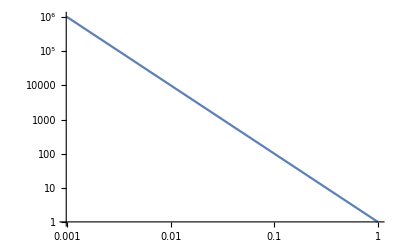

```mathematica
Plot[1/x^2,{x,0,1},ScalingFunctions->{"Log","Log"}]
```

Recalculated to the speed in parametric space: on the line we have distance s_parametric=√((Ω_f-Ω_i)^2+(Δ_f-Δ_i)^2)=20

```mathematica
parametricSpeed=20/TcOnδE2
```

3066.9 δE2

Generally comparable quantity is not T_c, but geodesical distance s=∫√(g_μν Λ^μ Λ^ν)

```mathematica
geodDistance[Ωg_]:=Module[{Ωscale,Ωlg,Δlg,t},
Ωscale=10;
Ωlg[t_]:=Ωg;
Δlg[t_]:=Ωscale (-1+2 t);
L=√({Δlg'[t],Ωlg'[t]}.g[Δlg[t],Ωlg[t]].{Δlg'[t],Ωlg'[t]});
NIntegrate[L,{t,0,(4a)/Ωg}]
]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t$142825 near {t$142825} = {0.55896}. NIntegrate obtained 17.7147 and 0.58743 for the integral and error estimates.

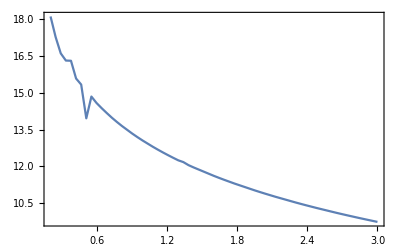

```mathematica
Plot[geodDistance[Ω],{Ω,0.2,3},PlotPoints->2,Frame->True,Evaluate@font,FrameLabel->MaTeX/@{"\\Omega","s"}]
```

Therefore critical geodesical speed v_c=s/T_c

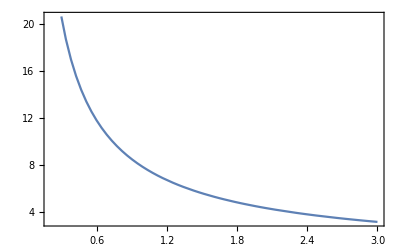

```mathematica
Plot[geodDistance[1/2 √(a/Tc)]/Tc,{Tc,0.2,3},PlotPoints->2,Frame->True,Evaluate@font,FrameLabel->MaTeX/@{"T_c","v_c"}]
```

## Finding zeros of the linear driving

### Analytics

```mathematica
inFidelityLinZeroCondition[t_,Tf_,Ωconst_]:=Module[{Ω,Δ,sqr,qq,gam,Δfi,Δi,u,T,ui,en,ent,enti,om,Q0,Q1,Q00,Q10,n,a0t,b0t},
Ω[T_]:=Ωconst;
Δ[T_]:=Δl[T/Tf];
sqr=√(Tf^-1 Δfi);
om=Ω[0]/sqr;

Δfi=Δ[Tf]-Δ[0];
Δi=Δ[0];

u[T_]:=Δ[T]/sqr;
ui=u[0];
en[T_]:=-√(Δ[T]^2+Ω[T]^2);
ent[T_]:=en[T]/sqr;

enti=ent[0];

(*Q0 and Q1 at initial time*)
qq=1/2 1/(√(enti(enti-om)));
Q00=qq(om-ui-enti);

Q10=qq(om+ui-enti);

n=(I om^2)/2;
gam=Gamma[1-n]/(√(2π));
a0t=gam(ParabolicCylinderD[n-1,(I-1)ui]Q00-(I+1)/om ParabolicCylinderD[n,(I-1)ui]Q10);
b0t=gam(ParabolicCylinderD[n-1,(1-I)ui]Q00+(I+1)/om ParabolicCylinderD[n,(1-I)ui]Q10);


Q0[T_]:=a0t ParabolicCylinderD[n,(1-I)u[T]]+b0t ParabolicCylinderD[n,(I-1)u[T]];
Q1[T_]:=-om/2(1-I)(a0t ParabolicCylinderD[n-1,(1-I)u[T]]-b0t ParabolicCylinderD[n-1,(I-1)u[T]]);
(*Real part needs to be added due to numerical error*)
Re[1/2(1+Δ[t]/en[t])-Δ[t]/en[t](Conjugate[Q0[t]]Q0[t]-Ω[0]/Δ[t] Re[Conjugate[Q0[t]]Q1[t]])]
]
```

### Numerics

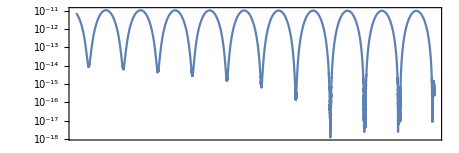

```mathematica
fidZOOMExport=Plot[inFidelityLinZeroCondition[Tf,Tf,0.3],{Tf,1880,1893},PlotRange->All,ScalingFunctions->{"Log","Log"},PerformanceGoal->"Quality",PlotPoints->1000,Evaluate@font,Frame->True,AspectRatio->1/3,ImageSize->460,FrameLabel->MaTeX/@{"T_f","1-F"}]
```

```mathematica
Export["/home/strelda/Documents/mff/dp/littleReports/twoLevelSystem/img/infidelityZoom.pdf",fidZOOMExport,"AllowRasterization"->True,ImageResolution->800];
```

```mathematica
fidZOOM=Plot[inFidelityLinZeroCondition[Tf,Tf,0.3],{Tf,1883,1893},PlotRange->All,ScalingFunctions->{"Log","Log"},PerformanceGoal->"Quality",PlotPoints->100,Evaluate@font,Frame->True,FrameLabel->MaTeX/@{"T_f","1-F"},AspectRatio->1/5,ImageSize->1500];
```

```mathematica
fidZOOMroots=ParallelTable[Quiet@FindRoot[inFidelityLinZeroCondition[Tf,Tf,0.3],{Tf,ttt},AccuracyGoal->Infinity,PrecisionGoal->100,WorkingPrecision->100],{ttt,1882,1892,1}]
```

{{Tf→1884.207728915528485521427217506756857453484336707575081582013819886137468113770306951519227214504166},{Tf→1886.710417583485396188151533401455847962244702951624579467841948448159246210806502459862727973123463},{Tf→1887.961761940770888649116151885484710758426289426894451015092049810574448133082142289663864504700549},{Tf→1889.213106313399173748846627360146251110741464703808843362425611789866251583304694146443468060737836},{Tf→1890.439553997632349197916243718893894306390411057357471750103108112131953725511270616794353835374108},{Tf→1890.489349075482691794638125811136393633767906682511590376045756325571324790285377374943631591589501},{Tf→1891.751348451934812279475706309243565395308256208322669780648141489278619994994112519556737445992481}}

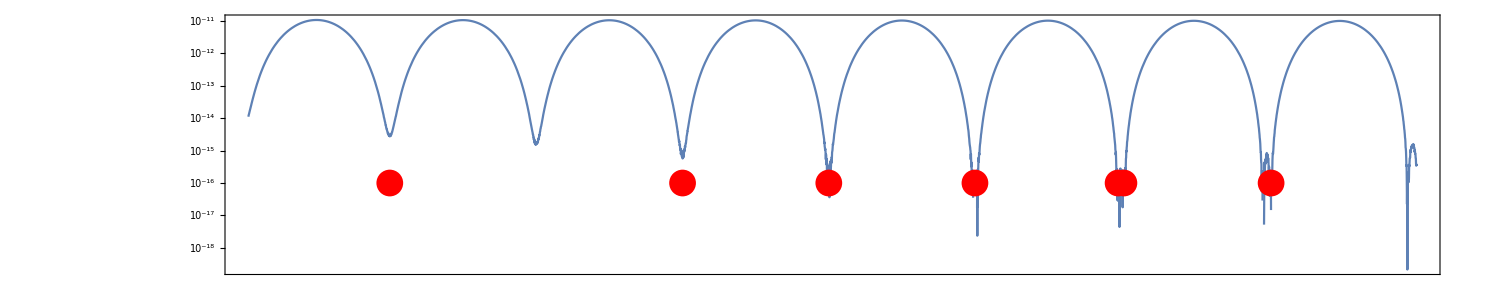

```mathematica
Show[{
fidZOOM,
ListPlot[Transpose@{Tf/.fidZOOMroots,ConstantArray[10^-16,Dimensions[fidZOOMroots][[1]]]},ScalingFunctions->{"Log","Log"},Evaluate@font,Frame->True,FrameLabel->MaTeX/@{"T_f","1-F"},PlotStyle->Red]
}]
```

```mathematica
periodeTab={{0.3,(1893-1883)/8},{0.6,(1893-1883)/16},{1.2,(1893-1883)/17},{3,(1893-1883)/20}} ;
```

#### => perioda=f(Ω,Tf)

### Minimas are in zero :

```mathematica
infidelityTfPlotLogZoom=Plot[-Log[1-inFidelityLin[Tf,Tf,0.3]],{Tf,1000,4000},PlotRange->All,ScalingFunctions->{"Log","Log"},PerformanceGoal->"Quality",PlotPoints->100,Evaluate@font,Frame->True,FrameLabel->{"t_final","-log(F)"}];
```

```mathematica
finalFidelityMinimasLin=Quiet@FindRoot[-Log[1-inFidelityLinNonC[Tf,Tf,0.3]],{Tf,#},WorkingPrecision->100]&/@Range[1500,3000,10];
```

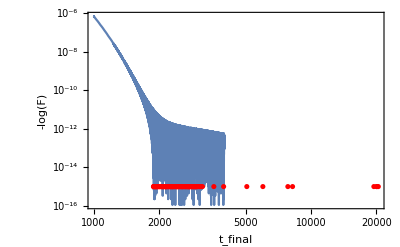

```mathematica
Show[{
infidelityTfPlotLogZoom,
ListPlot[Transpose@{Tf/.finalFidelityMinimasLin,ConstantArray[10^-15,Dimensions[finalFidelityMinimasLin][[1]]]},ScalingFunctions->{"Log","Log"},Evaluate@font,Frame->True,FrameLabel->{"t_final","1-F"},PlotStyle->Red]
}]
```

```mathematica
Table[Tf/.Min@FindRoot[-Log[1-inFidelityLinNonC[Tf,Tf,0.5]],{Tf,tff},WorkingPrecision->100],{tff,100,2000,400}]
```

FindRoot::precw: The precision of the argument function (-Log[0.999376-0.998752 (-0.05 Re[Times[«4»]]+Re[Conjugate[«1»] Plus[«2»]])]) is less than WorkingPrecision (100.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{1704.369295232520059831995790626059216785463892718679146474186486343743438717576050126220383585343626,637.4443257489672129941418722047940214096643450720577874437736510555823703933935588217559661279965931,899.7514689308153613619789434978322082006689840080199130318717643205550962186187968264434031628808922,1300.194790948595426486324030454377393273607173373016037133474207115343231486171447475068428618314307,1700.016647914308055251323845875878842797793082118491222669309769849358432046095092935666112020970787}

```mathematica
TcFromRootTab=ParallelTable[{Ω,Min[Table[Tf/.Quiet@FindRoot[-Log[1-inFidelityLinNonC[Tf,Tf,Ω]],{Tf,tff},WorkingPrecision->70],{tff,500,5000,200}]]},{Ω,0.3,1.5,0.1}];
```

```mathematica
(*TcFromRootTab=DeleteCases[TcFromRootTab,{om_,root_}/;root<0]*)
```

```mathematica
TcFromRootTab=TcFromRootTab[[2;;-1]];
```

-256.506/om^2+776.296/om

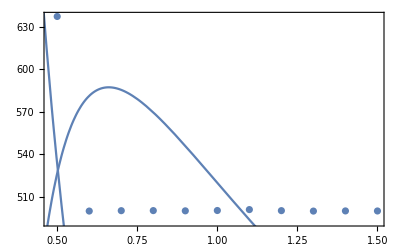

```mathematica
TcFromRootFit=Fit[TcFromRootTab,{om^-1,om^-2},om]
Show[{ListPlot[TcFromRootTab,Frame->True,PlotRange->All,FrameLabel->MaTeX/@{"\\Omega","T_c"}],Plot[TcFromRootFit,{om,0.1,3.0},PlotRange->All],
Plot[1.2 121.06976126016289/om^2-0.46 52.422291233262946/om,{om,0.1,3.0},PlotRange->All]}]
```

```mathematica
}
```

One can see that this dependence copies the boundary between singular and smooth behaviour in DensityPlot pretty nicely

```mathematica
Manipulate[Show[{dens2,ContourPlot[Tf==a 121/om^2+b 52/om,{om,0.1,5},{Tf,1,15000},PlotRange->All,ScalingFunctions->{"Log","Log","Log"}]}],{{a,1.2},0.1,10},{{b,-0.46},-5,5}]
```

## Fidelity slope

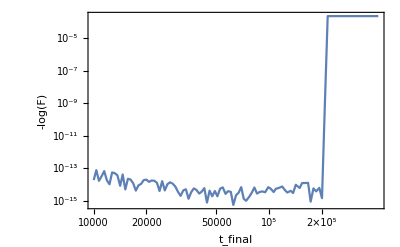

```mathematica
Plot[-Log[1-inFidelityLin[Tf,Tf,0.3]],{Tf,10^4,10^6},PlotRange->All,ScalingFunctions->{"Log","Log"},PerformanceGoal->"Quality",PlotPoints->3,Evaluate@font,Frame->True,FrameLabel->{"t_final","-log(F)"}]
```

```mathematica
Table[{k,Max[Table[Tf,{Tf,k,20+k}]]},{k,1,100,10}]
```

{{1,21},{11,31},{21,41},{31,51},{41,61},{51,71},{61,81},{71,91},{81,101},{91,111}}

```mathematica
smoothFidelity[Ω_,Ωmin_,Ωmax_,averageOverN_,qualityP_]:=Quiet@Table[{k,
Max@ParallelTable[-Log[1-inFidelityLin[Tf,Tf,Ω]],{Tf,k,averageOverN+k,qualityP}]},{k,200/Ω^2,Ωmax,averageOverN}]
```

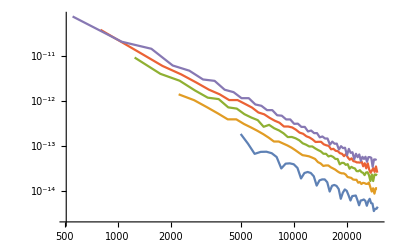

```mathematica
ListLinePlot[{
smoothFidelity[0.2,50/Ω^2,3 10^4,500,100],smoothFidelity[0.3,50/Ω^2,3 10^4,500,100],smoothFidelity[0.4,50/Ω^2,3 10^4,500,100],smoothFidelity[0.5,50/Ω^2,3 10^4,500,100],smoothFidelity[0.6,50/Ω^2,3 10^4,500,100]
},ScalingFunctions->{"Log","Log"}]
```

```mathematica
ListLinePlot[
Table[ParallelTable[-Log[1-inFidelityLin[Tf,Tf,om]],{Tf,1,10^4,1000}]%,{om,1.5,5,1}],
ScalingFunctions->{"Log","Log"}]
```

# Final fidelity vs max variance

maybe not doable generally

# ContourPlots for Lipkin, to see where is the chaotic and linear regime (3D ContourPlot will be needed). Or just choose some drivings with one parameter distance from singularity

## Define Hamiltonian

```mathematica
$Assumptions={λ∈Reals,χ∈Reals};
```

```mathematica
δ[a_,b_]:=KroneckerDelta[a,b];
Je[sn_,j_,m_]:=√(j(j+1)-m(m+sn 1));
```

```mathematica
V1[jp_,mp_,j_,m_]:=1/4(Je[1,j,m+1]Je[1,j,m]δ[mp,m+2]+Je[-1,j,m-1]Je[-1,j,m]δ[mp,m-2]+δ[mp,m](Je[-1,j,m]Je[1,j,m-1]+Je[1,j,m]Je[-1,j,m+1] ))
V2[jp_,mp_,j_,m_]:=1/2(m+j)(Je[1,j,m]δ[mp,m+1]+Je[-1,j,m]δ[mp,m-1])+1/2(m+1+j)Je[1,j,m]δ[mp,m+1]+1/2(m-1+j)Je[-1,j,m]δ[mp,m-1]
V3[jp_,mp_,j_,m_]:=δ[mp,m](j+m)^2
Hd[jp_,mp_,j_,m_]:=m δ[jp,j]δ[mp,m]-δ[jp,j]/(2j)(λ V1[jp,mp,j,m]+χ V2[jp,mp,j,m]+χ^2 V3[jp,mp,j,m])
```

```mathematica
nn=3;
```

```mathematica
jj=nn/2; 
dim=nn+1;
f[mp_,m_]:=Hd[jj,mp,jj,m];
HH=Table[f[mp,m],{mp,-jj,jj},{m,-jj,jj}];
H[λ_,χ_]=Table[f[mp,m],{mp,-jj,jj},{m,-jj,jj}];
HC=Compile[{{λ,_Real},{χ,_Real}},Evaluate@HH,Evaluate@compileOptions];
```

```mathematica
HH/.{λ->Ω[T],χ->Δ [T]}
```

{{-3/2+5/2 Cos[π T],-(5 Sin[π T])/(√3),(5 Cos[π T])/(√3),0},{-(5 Sin[π T])/(√3),-1/2+1/3 (35/2 Cos[π T]-100 Sin[π T]^2),-10 Sin[π T],(5 Cos[π T])/(√3)},{(5 Cos[π T])/(√3),-10 Sin[π T],1/2+1/3 (35/2 Cos[π T]-400 Sin[π T]^2),-(25 Sin[π T])/(√3)},{0,(5 Cos[π T])/(√3),-(25 Sin[π T])/(√3),3/2+1/3 (15/2 Cos[π T]-900 Sin[π T]^2)}}

```mathematica
EigensystemSorted[λ_?NumericQ,χ_?NumericQ]:=Module[{enNonSort,eigNonSort,en,eig},
{enNonSort,eigNonSort}=Eigensystem[HC[λ,χ],Method->{"Banded"}];
{en,eig}=Transpose@SortBy[Transpose[{enNonSort,eigNonSort}],First];
{en,eig}
]
```

### Fidelity functions

```mathematica
fLipkinLinear2[θ_,t_,Tf_]:=Module[{Ω,Δ,H,eig,Ψ,a,b,sol},
Ω[T_]:=Cos[θ] T/Tf;
Δ[T_]:=Sin[θ] T/Tf;
H[T_]:={{-1/2+5/2 Cos[π T],-5 Sin[π T]},{-5 Sin[π T],1/2+5/2 Cos[π T]-100 Sin[π T]^2}};
eig[T_]:=Eigenvectors[H[T]];
Ψ[T_]={a[T],b[T]};
sol=NDSolve[{I Ψ'[T]==H[T].Ψ[T],Ψ[0]=={1,0}},Ψ[T],{T,0,Tf},Method->{"TimeIntegration"->{"ExplicitRungeKutta"}}];
Fidelity[Flatten[Ψ[T]/.sol]/.T->t,eig[t][[1]]]
]
fLipkinLinear2[0,1,10]
```

0.997138

```mathematica
fLipkinLinear5[θ_,t_,Tf_]:=Module[{Ω,Δ,H,eig,Ψ,a,b,c,d,e,sol},
Ω[T_]:=Cos[θ] T/Tf;
Δ[T_]:=Sin[θ] T/Tf;
H[T_]:={{-2+5/2 Cos[π T],-5/2 Sin[π T],5/2 √(3/2) Cos[π T],0,0},{-5/2 Sin[π T],-1+1/4 (25 Cos[π T]-100 Sin[π T]^2),-5/2 (√(3/2)+√6) Sin[π T],15/4 Cos[π T],0},{5/2 √(3/2) Cos[π T],-5/2 (√(3/2)+√6) Sin[π T],1/4 (30 Cos[π T]-400 Sin[π T]^2),-5/2 (3 √(3/2)+√6) Sin[π T],5/2 √(3/2) Cos[π T]},{0,15/4 Cos[π T],-5/2 (3 √(3/2)+√6) Sin[π T],1+1/4 (25 Cos[π T]-900 Sin[π T]^2),-35/2 Sin[π T]},{0,0,5/2 √(3/2) Cos[π T],-35/2 Sin[π T],2+1/4 (10 Cos[π T]-1600 Sin[π T]^2)}};
eig[T_]:=Eigenvectors[H[T]];
Ψ[T_]={a[T],b[T],c[T],d[T],e[T]};
sol=NDSolve[{I Ψ'[T]==H[T].Ψ[T],Ψ[0]=={1,0,0,0,0}},Ψ[T],{T,0,Tf},Method->{"TimeIntegration"->{"ExplicitRungeKutta"}}];
Fidelity[Flatten[Ψ[T]/.sol]/.T->t,eig[t][[1]]]
]
fLipkinLinear5[1,1,10]
```

2.40225